## xBrauer : The algebra of traces and permutations.

```mathematica
xAct`xBrauer`$Version={"0.0.2",{2021,31,01}}
```

{0.0.2,{2021,31,1}}

```mathematica
xAct`xBrauer`$xTensorVersionExpected={"1.1.4",{2020,2,16}};
xAct`xBrauer`$xTrasVersionExpected={"1.0.6",{2014,10,30}};
```

## 1. Initialization

#### 1.0. TODO list

```mathematica
(** 1. Documentation **)
(** 2. Find Explicit formula for f-traceless projectors (Mathematical problem)**)
(** 3. Walled Brauer Projectors (Mathematical problem) **)
```

#### 1.1. GPL

```mathematica
(* xBrauer : Brauer Algebra; Traces and permutations *)

(* Copyright (C) 2020 T. Helpin *)

(* This program is free software; you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation; either version 2 of the License,or (at your option) any later version.

This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details.

*)
```

#### 1.2. Info package

```mathematica
(* :Title: xBrauer *)

(* :Author: Thomas Helpin *)

(* :Summary: Brauer Algebra; Traces and permutations. *)

(* :Brief Discussion:  *)
  
(* :Context: xAct`xBrauerNew` *)

(* :Package Version: 0.1.0 *)

(* :Copyright: T.Helpin (2020) *)

(* :History: TODO *)

(* :Keywords: TODO *)

(* :Source: xMAG.nb *)

(* :Warning: TODO *)

(* :Mathematica Version: 8.0 and later *)

(* :Limitations: *)
	
(* :Acknowledgements: *)
```

#### 1.3. BeginPackage

```mathematica
If[Unevaluated[xAct`xCore`Private`$LastPackage]===xAct`xCore`Private`$LastPackage,xAct`xCore`Private`$LastPackage="xAct`xBrauer`"];
```

```mathematica
xAct`xCore`Private`$LastPackage
```

xAct`xBrauer`

```mathematica
"xAct`xBrauer`"
```

xAct`xBrauer`

Explicit (not hidden) import of other packages:

```mathematica
Off[General::nostdvar]
Off[General::nostdopt]
BeginPackage["xAct`xBrauer`",{"xAct`xTras`","xAct`xTensor`","xAct`xPerm`","xAct`xCore`","xAct`ExpressionManipulation`","xAct`TraceFree`"}]
```

xAct`xBrauer`

```mathematica
"xAct`xBrauer`"
```

xAct`xBrauer`

```mathematica
"xAct`xBrauer`"
```

xAct`xBrauer`

```mathematica
"xAct`xBrauer`"
```

xAct`xBrauer`

Check version of xTensor. We simply compare dates:

```mathematica
If[Not@OrderedQ@Map[Last,{$xTensorVersionExpected,xAct`xTensor`$Version}],Throw@Message[General::versions,"xTensor",xAct`xTensor`$Version,$xTensorVersionExpected]]

If[Not@OrderedQ@Map[Last,{$xTrasVersionExpected,xAct`xTras`$Version}],Throw@Message[General::versions,"xTras",xAct`xTras`$Version,$xTrasVersionExpected]]
```

Welcome message:

```mathematica
Print[xAct`xCore`Private`bars]
Print["Package xAct`xBrauer`  version ",$Version[[1]],", ",$Version[[2]]];
Print["Copyright (C) 2020, Thomas Helpin, under the General Public License."];
```

------------------------------------------------------------

Package xAct`xBrauer`  version 0.0.2, {2021,31,1}

Copyright (C) 2020, Thomas Helpin, under the General Public License.

We specify the context xAct`xBrauer` to avoid overriding the Disclaimer of the other packages. However we need to turn off the message General:shdw temporarily:

```mathematica
Off[General::shdw]
xAct`xForm`Disclaimer[]:=Print["These are points 11 and 12 of the General Public License:\n\nBECAUSE THE PROGRAM IS LICENSED FREE OF CHARGE, THERE IS NO WARRANTY FOR THE PROGRAM, TO THE EXTENT PERMITTED BY APPLICABLE LAW. EXCEPT WHEN OTHERWISE STATED IN WRITING THE COPYRIGHT HOLDERS AND/OR OTHER PARTIES PROVIDE THE PROGRAM `AS IS.b4 WITHOUT WARRANTY OF ANY KIND, EITHER EXPRESSED OR IMPLIED, INCLUDING, BUT NOT LIMITED TO, THE IMPLIED WARRANTIES OF MERCHANTABILITY AND FITNESS FOR A PARTICULAR PURPOSE. THE ENTIRE RISK AS TO THE QUALITY AND PERFORMANCE OF THE PROGRAM IS WITH YOU. SHOULD THE PROGRAM PROVE DEFECTIVE, YOU ASSUME THE COST OF ALL NECESSARY SERVICING, REPAIR OR CORRECTION.\n\nIN NO EVENT UNLESS REQUIRED BY APPLICABLE LAW OR AGREED TO IN WRITING WILL ANY COPYRIGHT HOLDER, OR ANY OTHER PARTY WHO MAY MODIFY AND/OR REDISTRIBUTE THE PROGRAM AS PERMITTED ABOVE, BE LIABLE TO YOU FOR DAMAGES, INCLUDING ANY GENERAL, SPECIAL, INCIDENTAL OR CONSEQUENTIAL DAMAGES ARISING OUT OF THE USE OR INABILITY TO USE THE PROGRAM (INCLUDING BUT NOT LIMITED TO LOSS OF DATA OR DATA BEING RENDERED INACCURATE OR LOSSES SUSTAINED BY YOU OR THIRD PARTIES OR A FAILURE OF THE PROGRAM TO OPERATE WITH ANY OTHER PROGRAMS), EVEN IF SUCH HOLDER OR OTHER PARTY HAS BEEN ADVISED OF THE POSSIBILITY OF SUCH DAMAGES."]
On[General::shdw]
```

If xBrauer is not being called from other package then write this GPL short disclaimer:

```mathematica
If[xAct`xCore`Private`$LastPackage==="xAct`xBrauer`",
Unset[xAct`xCore`Private`$LastPackage];
Print[xAct`xCore`Private`bars];
Print["These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details."];
Print[xAct`xCore`Private`bars]]
```

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Note that symbols in the Global` context cannot be accessed while building the package:

```mathematica
$ContextPath
```

{xAct`xBrauer`,xAct`xTras`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,xAct`TraceFree`,System`}

```mathematica
{"xAct`xBrauer`","xAct`xTras`","xAct`xTensor`","xAct`xPerm`","xAct`xCore`","xAct`ExpressionManipulation`","xAct`TraceFree`","System`"}
```

{xAct`xBrauer`,xAct`xTras`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,xAct`TraceFree`,System`}

```mathematica
{"xAct`xMAG`","xAct`xTras`","xAct`xTensor`","xAct`xPerm`","xAct`xCore`","xAct`ExpressionManipulation`","xAct`TraceFree`","System`"}
```

{xAct`xMAG`,xAct`xTras`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,xAct`TraceFree`,System`}

```mathematica
$Context
```

xAct`xBrauer`

```mathematica
"xAct`xBrauer`"
```

xAct`xBrauer`

Established connection to external executable?

```mathematica
$xpermQ
```

True

#### 1.4. Non-standard setup

Here you would do things like:
Screen all dollar indices: (Currently deactivated)

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
SetOptions[ToRule,MetricOn->All,ContractMetrics->True]
```

{PatternIndices→All,TestIndices→True,MetricOn→All,UseSymmetries→True,Verbose→False,ContractMetrics→True,Evaluate→False}

#### 1.5. Usage messages

Here we declare the usage messages. This also creates the variables in the public scope.

```mathematica
(*** VERSIONS ***)

$Version::usage="$Version is a global variable giving the version of the package xBrauer in use.";

$xTensorVersionExpected::usage="$xTensorVersionExpected is a global variable giving the oldest possible version of the package xTensor which is required by the version of the package xBrauer in use.";

$xTrasVersionExpected::usage="$xTrasVersionExpected is a global variable giving the oldest possible version of the package xPert which is required by the version of the package xBrauer in use.";
```

```mathematica
(** Reserverd words in xBrauer **)
```

```mathematica
(*** Heads ****)
BrauerList::usage="BrauerList is the head for the List associated to a Brauer diagram. The list is a order disjoint union of pair partitions.";
BrauerGraph::usage="BrauerGraph is the head for the Graph associated to a Brauer diagram";
BrauerTab::usage="BrauerTab is the head for the list associated to a Young tableau filled with numbers 1,2 and 3. BrauerTableaux label the conjugacy classes obtained by averaging diagrams with \
the symmetric group in the Brauer Algebra. The numbers 1,2, and 3 represente North arcs, South arcs, and Propagating lines respectively.\
 Cf: O.King, P.Martin, and A.Parker : Journal of Algebra 512, 20 (2018) and also Shalile, A. On the Center of the Brauer Algebra. Algebr Represent Theor 16, 65–100 (2013).";
(*** Brauer Diagram/List ***)
SymmetricGroupQ::usage="SymmetricGrouQ[brauerlist] returns True if brauerlist represent a permutation, False otherwise.";
PermToBrauer::usage="PermToBrauer[degree,perm] transform a permutation in xPerm notation (Perm/Cycles) into a BrauerList";
PermNotation::usage="PermNotation is an options of BrauerToPerm. It must be either Cycles or Perm.";
BrauerToPerm::usage="BrauerToPerm[brauerlist] transform a permutation in the brauerlist form into a (Perm/Cycles) in xPerm notation.";
BrauerDiagram::usage =
	"BrauerDiagram[degree,{{arcsup},{arcsdown},{lines}}]/BrauerDiagram[BrauerList[{{arcsup},{arcsdown},{lines}}]] returns a BrauerGraph object \
corresponding to the list in the argument.";
BrauerDiagramToList::usage="BrauerDiagramToList[dia] returns the BrauerList associated to dia.";
BrauerElements::usage="BrauerElements[n] returns a list of all the elements of Brauer on n vertex,\
 namely the elements of the set of the disjoint union of pair partitions on 2n symbols.";
IdentityBrauer::usage="IdentityBrauer[n] returns the identiy in B(n) in a the form of a BrauerList.";
(** Generators of the Brauer monoid ***)
BrauerGenerators::usage="BrauerGenerators[degree] generates the list of the generators of the Brauer monoïd B(degree).";
SymmetricGroupOnly::usage="SymmetricGroupOnly is a booleen option for BrauerTableaux, ConjugacyClassRelations.";
(** Multiplication in Brauer **)
BrauerProduct::usage="BrauerProduct[diag1,diag2] return the product diagram of diag1 with diag2, BrauerProduct[list1,list2] returns/
 the product list of list1 with list2.";
dtrace::usage="The scalar resulting from the contraction of two arcs in the Brauer product";
OutputBrauer::usage="OutputBrauer is a booleen option for ConjugacyClassSum and for SymmetryGroupAverage. Its value can be either Graph or List.";

(****************************************************************************************)
(************************** Tools from the symmetric Group ******************************)
(****************************************************************************************)

(******** Young operators and seminormal Young Operators ****)
StdTableaux::usage="StdTableaux[n] return a list of all standard Young tableaux associated with the partition of n.";
TransposePartition::usage="TransposePartition[IntegerPartition] return the transpose partition.";
TransposeTableau::usage="TransposeTableau[tableau] returns the transpose young tableau of tab.";
DimOfDiagram::usage="DimOfDiagram[part] returns the dimension of the irrep associated to the young diagram corresponding the partition part.";
NumOfTableaux::usage="NumOfTableaux[n] returns the numbers of standard tableau for the partitions of the integer n.";
YoungProjector::usage="YoungProjector[standardtableau] returns the Young projector associated to the standard tableau.";
BratteliPath::usage="BratteliPath[standardtableau] returns the path of a standard tableau in a Bratteli diagram.";
SNYoungProjector::usage="SNYoungProjector[stdtab] returns the semi-normal Young projector associated to the standard tableau stdtab.";
YoungSymmetrizer::usage"ss.";
YoungAntisymmetrizer::usage"sss.";
YoungProject2::usage"YoungProject2[exp,tab] projects the tensorial expression expr onto the Young tableau tab using the Young Projector";
SNYoungProject::usage"SNYoungProject[exp,tab] projects the tensorial expression expr onto the Young tableau tab using the Seminormal Young Projector";

(****************************************************************************************)
(***************** Conjugacy classes in Brauer and Traceless projectors *****************)
(****************************************************************************************)

(**** Equivalence class of brauer diagrams averaging with the symmetric group ***)
TableauForm::usage="Transform a list into a young tableau format";
BrauerTableaux::usage="BrauerTableaux[degree,narcs] BrauerTab[degree,narcs] returns a list of the conjugacy class for Brauer(degree) with narcs arcs in a form of NSP Young tableaux,\
 where north arcs (N) are represented by 1 south arcs (S) by 2 and propagating lines (P) by 3.";
NumberOfBrauerTab::usage="NumberOfBrauerTab[n] returns the number of conjugacy class in Brauer on n vertices.";
ConjugacyClass::usage="ConjugacyClass[brauerlist] returns a list of the elements in the same (symmetric group) conjugacy class as brauerlist. It is also a booleen option for brauer product.
It increase the speed when one is interested by the product of class sum ";
ConjugacyClassSum::usage="ConjugacyClassSum[diag] generate the sum of symmetric group conjugate diagrams of diag.";
SymmetricGroupAverage::usage="SymmetricGroupAverage[diagBrau,n1,n2] generate a list of diagrams corresponding to every permutations of nodes n1 to n2";
NormalizeClass::usage="NormalizeClass is a booleen option for GenerateConjugateDiagrams and GenerateConjugateList.";
BrauerTabToRep::usage="TableauToRepDiagram[NSPtableau] yield the representative diagram corresponding to the NSP tableau.";
MergeBrauer::usage="MergeBrauer[brauerlist1,brauerlist2] glue brauerlist 1 and brauerlist 2 together.";
(****************************************************************************************)
(***************************** HyperOctahedral Group ************************************)
(****************************************************************************************)
HyperOctahedralQ::usage="To do";
HyperOctahedralGenerators::usage="To do";
HyperOctahedralGroup::usage="To do";
CosetType::usage="To do";
(****************************************************************************************)
(***************************** Weingarten Calculus **************************************)
(****************************************************************************************)
(** Characters of the symmetric group : From the Package IntU by Zbigniew Puchala **)
CharacterSymmetricGroup::usage="To do";
CycleType::usage="To do";
(** Weingarten function *)
ZonalSpherical::usage="To do";
ZonalPolynomialId::usage="To do";
WeingartenO::usage="To do";
SchurPolynomialId::usage="To do";
WeingartenU::usage="To do";
(****************************************************************************************)
(**************** Algebra of Conjugacy classes and Traceless projectors *****************)
(****************************************************************************************)
 
IdealSpace::usage="IdealSpace is booleen option for ConjugacyClassRelations. Let J(m) in B(n) be the space of diagram with at least m arcs.\
Then there a chain of ideals in the Brauer algebra : J(n) in J(n-1) in ... in J(1) in J(0)=B(n).";
FactorSpace::usage="FactorSpace is booleen option for ConjugacyClassProduct and ConjugacyClassRelations. One can define a product in the factor space consisting of \
diagram with exaclty m arcs : J[m]=J(m)/J(m+1). For example the symmetric group algebra is B(n)/J(1).";
ConjugacyClassProduct::usage="ConjugacyClassProduct[tab1,tab2], performs the product the conjugacy class sum associated to the brauer tableau tab1\
 with the one associated to the brauer tableau tab2.";
ConjugacyClassRelations::usage="ConjugacyClassRelations[tab] returns all product rules between tab and others classes in the algebra.";
SplittingIdempotent::usage="SplittingIdempotent[n,f] returns the splitting idempotent corresponding to the short sequence 0->J(f)->B(n)->B(n)/J(f).";
TraceProjector::usage="TraceProjector[n,f] returns the f-trace projector in Brauer(n). The f-trace projector can be understood as the identity in J(f) the space of diagram with at least f arcs.";
TraceLessProjector::usage="TraceLessProjector[n,f] returns the f-traceless projector in Brauer(n).";
ToTraceTensor::usage="ToTraceTensor[tens,f] projects tens onto the space of f-trace tensors using TraceProjector[n,f] where n is the order of tens.";
ToTracelessTensor::usage="ToTracelessTensor[tens,f] projects tens onto the space of f-traceless tensors using TraceLessProjector[n,f] where n is the order of tens.";

(****************************************************************************************)
(*************************** Realization on tensors *************************************)
(****************************************************************************************)

TensorToBrauer::usage="TensorToBrauerDiagram[metricexp] transforms products of metrics into Brauer diagrams or Brauer lists.";
BrauerToTensor::usage="BrauerDiagramToTensor[diag/list,met] transforms a brauer diagram/list into a product of metrics met. 
Vertex in the upper part are converted to UpIndex and vertex in the lower part are converted to DownIndex";

(****************************************************************************************)
(******************************* Walled Brauer part          ****************************)
(****************************************************************************************)

(****************************************************************************************)
(******************************* Some Tools in developpement ****************************)
(****************************************************************************************)

(** Jucys Murphy elements in the Brauer Algebra **)
JucysMurphySymbol::usage="JucysMurphySymbol[order] generates a list of symbols for the Jucys-Murphys elements of B(order).";
JucysMurphy::usage="JucysMurphy[order] generates a list of JM elements of B(order).";
JucysMurphySymbolToList::usage="Convert the JM symbol into JM Brauerlist";
(********** Pairs of Cycles for classes of Brauer with one arcs ***)
SplitBrauerDiagram::usage="SplitBrauerDiagram[diag] decomposes diag into its sub diagrams having independent cycles. It can also be applied to Brauer Lists";
ToCyclesGraph::usage="ToCyclesGraph[diag] returns the cycles digrams associated to the Brauer diagram diag. It can also be applied to Brauer Lists";
```

#### 1.6. Begin private

```mathematica
Begin["`Private`"]
```

xAct`xBrauer`Private`

```mathematica
"xAct`xBrauer`Private`"
```

xAct`xBrauer`Private`

The reserved words in version 0.1.0 :

```mathematica
Names["xAct`xBrauer`*"]
```

{BratteliPath,BrauerDiagram,BrauerDiagramToList,BrauerElements,BrauerGenerators,BrauerGraph,BrauerList,BrauerProduct,BrauerTab,BrauerTableaux,BrauerTabToRep,BrauerToPerm,BrauerToTensor,CharacterSymmetricGroup,ConjugacyClass,ConjugacyClassProduct,ConjugacyClassRelations,ConjugacyClassSum,CosetType,CycleType,DimOfDiagram,dtrace,FactorSpace,HyperOctahedralGenerators,HyperOctahedralGroup,HyperOctahedralQ,IdealSpace,IdentityBrauer,JucysMurphy,JucysMurphySymbol,JucysMurphySymbolToList,MergeBrauer,NormalizeClass,NumberOfBrauerTab,NumOfTableaux,OutputBrauer,PermNotation,PermToBrauer,SchurPolynomialId,SNYoungProject,SNYoungProjector,SplitBrauerDiagram,SplittingIdempotent,StdTableaux,SymmetricGroupAverage,SymmetricGroupOnly,SymmetricGroupQ,TableauForm,TensorToBrauer,ToCyclesGraph,ToTracelessTensor,ToTraceTensor,TraceLessProjector,TraceProjector,TransposePartition,TransposeTableau,WeingartenO,WeingartenU,YoungAntisymmetrizer,YoungProject2,YoungProjector,YoungSymmetrizer,ZonalPolynomialId,ZonalSpherical,$Version,$xTensorVersionExpected,$xTrasVersionExpected}

```mathematica
%//Length
```

67

```mathematica
$ContextPath
```

{xAct`xBrauer`,xAct`xTras`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,xAct`TraceFree`,System`}

```mathematica
{"xAct`xBrauer`","xAct`xTras`","xAct`xTensor`","xAct`xPerm`","xAct`xCore`","xAct`ExpressionManipulation`","xAct`TraceFree`","System`"}
```

{xAct`xBrauer`,xAct`xTras`,xAct`xTensor`,xAct`xPerm`,xAct`xCore`,xAct`ExpressionManipulation`,xAct`TraceFree`,System`}

```mathematica
$Context
```

xAct`xBrauer`Private`

```mathematica
"xAct`xBrauer`Private`"
```

xAct`xBrauer`Private`

Now this is not being used. Deactivated cell :

```mathematica
BeginExamples[]:=(Set[$Context,"Global`"];Global`symbols=Names["Global`*"];Null)
Global`EndExamples[]:=(If[#=!={},Print["There are new symbols in Global`:",#]];Set[$Context,"xAct`xForm`Private`"];Null)&@Complement[Names["Global`*"],Global`symbols]
```

### a. Function associated to the Graphical representation of diagrams and cycles

```mathematica
vertexcoordinates::usage="xBrauer`Private`vertexcoordinates[{1,2,3,..,n}].";
BrauerListToEdges::usage="xBrauer`Private`BrauerListToEdges[{arcsup},{arcsdown},{lines}].";
ESF::usage="xBrauer`Private`ESF[edge,range1,range2] is the EdegeShapeFunction for Brauer diagrams.";
VLF::usage="xBrauer`Private`VLF[edgelist] is the VertexLabelFunction for Brauer Cycles diagrams.";
```

### b. Information related to a diagram

```mathematica
EdgesToArcsUpList::usage="xBrauer`Private`EdgesToArcsUpList[range,edgelist] yield a list of arcs in the upper level of a diagram";
EdgesToArcsDownList::usage="xBrauer`Private`EdgesToArcsUpList[range,edgelist]  yield a list of arcs in the down level of a diagram";
EdgesToLinesList::usage="xBrauer`Private`EdgesToLinesList[range1,range2,edgelist]  yield a list of lines between the two level of a diagram";
```

## 2. Definition of Brauer Diagrams as a Graph object

### 2.1. Local (private) function

```mathematica
vertexcoordinates[vertlist_]:=With[{lvertlist=Length[vertlist]},
With[{halflvertlist=lvertlist/2,step2=(lvertlist/2+1)},
Block[{vertlistpart},
vertlistpart=Partition[vertlist,halflvertlist];
Join[Map[#->{#-1,1}&,vertlistpart[[1]]],Map[#->{#-step2,-1}&,vertlistpart[[2]]]]
]
]
];
BrauerListToEdges[positionarcs1_List,positionarcs2_List,positionline_]:=Map[UndirectedEdge[#[[1]],#[[2]]]&,Join[positionarcs1,positionarcs2,positionline]];
ESF[edge_List,range1_,range2_]:=With[{edgelist=EdgesToList[edge]},
Join[Map[#->GraphElementData[{"CurvedArc","Curvature"->-1.1/(#[[2]]-#[[1]])-0.1}]&,Map[#[[1]]->#[[2]]&,EdgesToArcsUpList[range1,edgelist]]],Map[#->GraphElementData[{"CurvedArc","Curvature"->1.1/(#[[2]]-#[[1]])+0.1}]&,Map[#[[1]]->#[[2]]&,EdgesToArcsDownList[range2,edgelist]]]]];

EdgesToList[edges_]:=Map[{#[[1]],#[[2]]}&,edges];
EdgesToArcsUpList[range_,edgeslist_]:=Select[edgeslist,MemberQ[range,#[[1]]]&&MemberQ[range,#[[2]]]&];
EdgesToArcsDownList[range_,edgeslist_]:=
Select[edgeslist,MemberQ[range,#[[1]]]&&MemberQ[range,#[[2]]]&];
EdgesToLinesList[range1_,edgeslist_]:=
Select[edgeslist,MemberQ[range1,#[[1]]]&&MemberQ[range1+Length[range1],#[[2]]]&];
```

### 2.2. The Function which creates the Brauer diagram as a Graph object

```mathematica
(*** Output Format ***)
```

```mathematica
BrauerList/:MakeBoxes[BrauerList[blist_List],StandardForm]:=SubscriptBox[MakeBoxes[blist,StandardForm],"B"];
BrauerGraph/:MakeBoxes[BrauerGraph[bgraph_Graph],StandardForm]:=SubscriptBox[MakeBoxes[bgraph,StandardForm],SubscriptBox["B","g"]];
MakeExpression[SubscriptBox[b_,"B"],StandardForm]:=MakeExpression[RowBox[{"BrauerList","[",b,"]"}],StandardForm];
MakeExpression[SubscriptBox[b_,SubscriptBox["B","g"]],StandardForm]:=MakeExpression[RowBox[{"BrauerGraph","[",b,"]"}],StandardForm];
```

1. The function

```mathematica
dtrace:=ToExpression["d"];
```

```mathematica
Options[BrauerDiagram]:={VertexSize->Tiny,ImageSize->Tiny,EdgeStyle->Automatic}
BrauerDiagram[degree_Integer,{positionarcs1_List,positionarcs2_List,positionline_List},options:OptionsPattern[]]:=With[{range=Range[2*degree],range1=Range[degree]},
With[{range2=range1+degree,edges=BrauerListToEdges[positionarcs1,positionarcs2,positionline]},
Block[{brauerdiagram,imagesize,vertexsize,edgestyle},
{imagesize}=OptionValue[{BrauerDiagram},{options},{ImageSize}];
{vertexsize}=OptionValue[{BrauerDiagram},{options},{VertexSize}];
{edgestyle}=OptionValue[{BrauerDiagram},{options},{EdgeStyle}];
brauerdiagram=BrauerGraph[Graph[range,edges,{VertexCoordinates->vertexcoordinates[range],EdgeShapeFunction ->ESF[edges,range1,range2],EdgeStyle->edgestyle,VertexSize->vertexsize, ImageSize ->imagesize}]]]]
];
```

```mathematica
BrauerDiagram[{positionarcs1_List,positionarcs2_List,positionline_List},options:OptionsPattern[]]:=BrauerDiagram[(Length[positionarcs1]*2+Length[positionline]),{positionarcs1,positionarcs2,positionline},options];
```

```mathematica
BrauerListToListDiagram[blist_BrauerList]:=Module[{n=Length[Flatten[Sequence@@blist]],list=Sequence@@blist,range1,range2,arcsup,arcsdown,lines},
range1=Range[n/2];
range2=range1+n/2;
arcsup=EdgesToArcsUpList[range1,list];
arcsdown=EdgesToArcsDownList[range2,list];
lines=EdgesToLinesList[range1,list];
Sort/@{arcsup,arcsdown,lines}
];
```

```mathematica
(** Algebra **)
```

```mathematica
BrauerDiagram[brauerlist_BrauerList,options:OptionsPattern[]]:=BrauerDiagram[BrauerListToListDiagram[ brauerlist],options];
BrauerDiagram[exp_Plus,options:OptionsPattern[]]:=BrauerDiagram[#,options]&/@exp;
BrauerDiagram[Times[n_?NumberQ,brauerlist_BrauerList],options:OptionsPattern[]]:=Times[n,BrauerDiagram[brauerlist,options]]
BrauerDiagram[Times[n_Times,brauerlist_BrauerList],options:OptionsPattern[]]:=Times[n,BrauerDiagram[brauerlist,options]]
BrauerDiagram[Times[n_Symbol,brauerlist_BrauerList],options:OptionsPattern[]]:=Times[n,BrauerDiagram[brauerlist,options]]
BrauerDiagram[Times[n_Power,brauerlist_BrauerList],options:OptionsPattern[]]:=Times[n,BrauerDiagram[brauerlist,options]]
```

```mathematica
BrauerDiagram[0,options:OptionsPattern[]]:=0;
```

2. From Brauer diagram to its associated list

```mathematica
BrauerDiagramToList[bgraph_BrauerGraph]:=BrauerList[Sort[List@@@EdgeList@(Sequence@@bgraph)]];
```

```mathematica
BrauerDiagramToList[Times[n_,bgraph_BrauerGraph]]:=Times[n,BrauerDiagramToList[bgraph]];
BrauerDiagramToList[exp_Plus]:=BrauerDiagramToList/@exp;
```

3. Elements in Brauer(n) : Algorithm working up Brauer(8).

```mathematica
(***** Source Code :: https://mathematica.stackexchange.com/questions/88085/find-all-the-possible-ways-of-partitioning-a-list-into-a-set-of-pairs-of-element   ****)
```

```mathematica
genIdx[n_?EvenQ]:=Flatten@With[{r=Range@n},Fold[With[{l1=#,l2=#2},Flatten[Map[With[{la=#,c=Complement[r,#]},Join[la,c[[#]]]&/@l2]&,l1],1]]&,Subsets[Range@#,{2},#-1]&/@Range[#,2,-2]&@n]];
xformLst[lst_,idx_]:=If[(Length@lst*(Length@lst-1)!!)==Length@idx,With[{l=Length@lst},ArrayReshape[lst[[idx]],{(l-1)!!,l/2,2}]],Abort[]];
```

```mathematica
BrauerElements[n_]:=BrauerList/@xformLst[Range[2*n],genIdx[2*n]];
```

4. Counting number of arcs : private for now

```mathematica
NumberOfArcs[blist_BrauerList]:=Count[Sequence@@blist,a_/;a[[1]]>Length[Sequence@@blist]]
```

### 2.3. xPerm to BrauerList formalism and BrauerList to Cycles

```mathematica
SymmetricGroupQ[blist_BrauerList]:=AllTrue[Sequence@@blist,MemberQ[Range[Length[Sequence@@blist]]+Length[Sequence@@blist],#[[2]]]&];
```

```mathematica
(* Convertion Mathematica <-> xPerm notation for cycles *)
```

```mathematica
ToSystemCycles[cycs_Cycles]:=System`Cycles@@({{Sequence@@cycs}});
ToxPermCycles[cycs_System`Cycles]:=Cycles@@(Sequence@@cycs);
```

```mathematica
(** Mathematica and xPerm notation for Permutation to Brauer notation **)
```

```mathematica
PermToBrauer[perm_?PermutationListQ]:=BrauerList[MapThread[{#1,#2}&,{Range[Length[perm]],Permute[Range[Length[perm]]+Length[perm],perm]}]];
PermToBrauer[perm_Perm]:=PermToBrauer[Sequence@@perm];
PermToBrauer[perm_System`Cycles,len_Integer]:=PermToBrauer[PermutationList[perm,len]];
PermToBrauer[perm_Cycles,len_Integer]:=PermToBrauer[ToSystemCycles@perm,len];
```

```mathematica
(** Algebra **)
```

```mathematica
PermToBrauer[Times[n_?NumberQ,exp_Plus]]:=Times[n,PermToBrauer[exp]];
PermToBrauer[Times[n_?NumberQ,exp_Plus],len_Integer]:=Times[n,PermToBrauer[exp,len]];
PermToBrauer[Times[n_?NumberQ,perm_/;(SameQ[Head[perm],List]||SameQ[Head[perm],Perm])]]:=Times[n,PermToBrauer[perm]];
PermToBrauer[Times[n_Times,perm_/;(SameQ[Head[perm],List]||SameQ[Head[perm],Perm])]]:=Times[n,PermToBrauer[perm]];
PermToBrauer[Times[n_Symbol,perm_/;(SameQ[Head[perm],List]||SameQ[Head[perm],Perm])]]:=Times[n,PermToBrauer[perm]];
PermToBrauer[exp_Plus,len_Integer]:=PermToBrauer[#,len]&/@exp;
PermToBrauer[exp_Plus]:=PermToBrauer/@exp;
```

```mathematica
Options[BrauerToPerm]:={PermNotation->Perm}
BrauerToPerm[brauerlist_?SymmetricGroupQ,options:OptionsPattern[]]:=Module[{perm,permnotation},
{permnotation}=OptionValue[{BrauerToPerm},{options},{PermNotation}];
perm=Perm[Map[#[[2]]&,Sequence@@brauerlist]-Length[Sequence@@brauerlist]];
If[permnotation===Perm,
Return[perm,Module],
Return[TranslatePerm[perm,Cycles],Module]]
];
```

The identity :

```mathematica
IdentityBrauer[n_Integer]:=PermToBrauer[Range[n]];
```

## 3. Product between BrauerList/BrauerGraph

1. The rule for product

```mathematica
rulesbrauerproduct={{a___,{u_,x_},b___,{v_,x_},c___}:>{{u,v},a,b,c},{a___,{x_,u_},b___,{x_,v_},c___}:>{{u,v},a,b,c},{a___,{x_,u_},b___,{v_,x_},c___}:>{{u,v},a,b,c},{a___,{u_,x_},b___,{x_,v_},c___}:>{{u,v},a,b,c}};
```

```mathematica
rulesbrauerproduct12={{{u_,x_},a___,{v_,x_},b___}:>{{u,v},a,b},{{u_,x_},a___,{x_,v_},b___}:>{{u,v},a,b}};
```

2. The function for the product of two Brauer List

If both lists belong to the symmetric group we use PermProduct which is much more efficient than the BrauerProduct function.

```mathematica
BrauerProduct[Brauerlist1_?SymmetricGroupQ,Brauerlist2_?SymmetricGroupQ,options:OptionsPattern[]]:=PermToBrauer[PermProduct[BrauerToPerm[Brauerlist1],BrauerToPerm[Brauerlist2]]];
```

```mathematica
Options[BrauerProduct]:={ImageSize->Tiny,ConjugacyClass->False}
BrauerProduct[Brauerlist1_BrauerList,Brauerlist2_BrauerList,dbrauer___,options:OptionsPattern[]]:=Module[{brauerlist1=Sequence@@Brauerlist1,brauerlist2=Sequence@@Brauerlist2,degdiag,arcsup,arcsdown,nloops,listproddiag,listproddiagnl,prodbrauerlist,conjproduct},
{conjproduct}=OptionValue[{BrauerProduct},{options},{ConjugacyClass}];
degdiag=Length[brauerlist1];
(*********************************************************)
(**************** The general product ********************)
(*********************************************************)
arcsup=EdgesToArcsUpList[Range[degdiag],brauerlist2];
arcsdown=EdgesToArcsDownList[Range[degdiag]+degdiag,brauerlist1];
listproddiagnl=Join[Complement[brauerlist2,arcsup],Complement[brauerlist1,arcsdown]+degdiag];
If[MemberQ[brauerlist2,{1,2}]||!conjproduct,
listproddiagnl=listproddiagnl//.rulesbrauerproduct;
(***** Taking care of loops *****)
listproddiag=DeleteCases[listproddiagnl,{a_,a_}];
nloops=Length[listproddiagnl]-Length[listproddiag];
(**** We sort the list and substract degdiag to the vertex which corresponded to the bottom diagram **********)
listproddiag=Partition[If[Greater[#,2*degdiag],#-degdiag,#]&/@Flatten@listproddiag,2];
listproddiag=Map[Sort[#,#1<#2&]&,listproddiag];
prodbrauerlist=BrauerList[Sort@Join[arcsup,listproddiag,arcsdown]];
Return[dbrauer^nloops*prodbrauerlist,Module]
];
(**********************************************************************************************************************************************************************)
(******** Product of Two conjugacy class sum : part of the product is now "truncated" because of the standard form of the conjugacy class representatives  ************)
(**********************************************************************************************************************************************************************)
listproddiagnl=listproddiagnl//.rulesbrauerproduct12;
If[!SameQ[listproddiagnl[[1,2]],2],
Return[Nothing,Module]];
listproddiagnl=listproddiagnl//.rulesbrauerproduct;
(***** Taking care of loops *****)
listproddiag=DeleteCases[listproddiagnl,{a_,a_}];
nloops=Length[listproddiagnl]-Length[listproddiag];
(**** We sort the list and substract degdiag to the vertex which corresponded to the bottom diagram **********)
listproddiag=Partition[If[Greater[#,2*degdiag],#-degdiag,#]&/@Flatten@listproddiag,2];
listproddiag=Map[Sort[#,#1<#2&]&,listproddiag];
prodbrauerlist=BrauerList[Sort@Join[arcsup,listproddiag,arcsdown]];
dbrauer^nloops*prodbrauerlist
]
```

```mathematica
BrauerProduct[brauerlist2_BrauerList,brauerlist1_BrauerList,options:OptionsPattern[]]:=BrauerProduct[brauerlist2,brauerlist1,dtrace,options]
```

```mathematica
(*********** Product in the algebra ****************)
```

```mathematica
BrauerProduct[list1_List,list2_List,options:OptionsPattern[]]:=Plus@@(BrauerProduct[#[[1]],#[[2]],options]&/@Tuples[{list1,list2}]);
```

```mathematica
BrauerProduct[exp1_Plus,exp2_Plus,options:OptionsPattern[]]:=BrauerProduct[List@@exp1,List@@exp2,options];
BrauerProduct[brauerlist2_BrauerList,exp_Plus,options:OptionsPattern[]]:=BrauerProduct[brauerlist2,#,options]&/@exp;
BrauerProduct[exp_Plus,brauerlist2_BrauerList,options:OptionsPattern[]]:=BrauerProduct[#,brauerlist2,options]&/@exp;
BrauerProduct[brauerlist2_BrauerList,Times[n_?NumberQ,brauerlist1_BrauerList],options:OptionsPattern[]]:=Times[n,BrauerProduct[brauerlist2,brauerlist1,options]];
BrauerProduct[Times[n_?NumberQ,brauerlist1_BrauerList],brauerlist2_BrauerList,options:OptionsPattern[]]:=Times[n,BrauerProduct[brauerlist1,brauerlist2,options]];
BrauerProduct[Times[n1_?NumberQ,brauerlist1_BrauerList],Times[n2_?NumberQ,brauerlist2_BrauerList],options:OptionsPattern[]]:=Times[n1*n2,BrauerProduct[brauerlist1,brauerlist2,options]];
BrauerProduct[brauerlist2_BrauerList,Times[n_Symbol,brauerlist1_BrauerList],options:OptionsPattern[]]:=Times[n,BrauerProduct[brauerlist2,brauerlist1,options]];
BrauerProduct[Times[n_Symbol,brauerlist1_BrauerList],brauerlist2_BrauerList,options:OptionsPattern[]]:=Times[n,BrauerProduct[brauerlist1,brauerlist2,options]];
BrauerProduct[Times[n1_Symbol,brauerlist1_BrauerList],Times[n2_Symbol,brauerlist2_BrauerList],options:OptionsPattern[]]:=Times[n1*n2,BrauerProduct[brauerlist1,brauerlist2,options]];
BrauerProduct[Times[n1_Times,brauerlist1_BrauerList],Times[n2_Times,brauerlist2_BrauerList]]:=Times[n1*n2,BrauerProduct[brauerlist1,brauerlist2]];
BrauerProduct[Times[n1_Times,brauerlist1_BrauerList],brauerlist2_BrauerList]:=Times[n1,BrauerProduct[brauerlist1,brauerlist2]];
BrauerProduct[brauerlist1_BrauerList,Times[n2_Times,brauerlist2_BrauerList]]:=Times[n2,BrauerProduct[brauerlist1,brauerlist2]];
BrauerProduct[Times[n1_Times,brauerlist1_BrauerList],n2_*brauerlist2_BrauerList]:=Times[n1*n2,BrauerProduct[brauerlist1,brauerlist2]];
BrauerProduct[n1_*brauerlist1_BrauerList,Times[n2_Times,brauerlist2_BrauerList]]:=Times[n2*n1,BrauerProduct[brauerlist1,brauerlist2]];
BrauerProduct[n1_*brauerlist1_BrauerList,Times[n2_Times,brauerlist2_BrauerList]]:=Times[n2*n1,BrauerProduct[brauerlist1,brauerlist2]];
BrauerProduct[exp1_Times,exp2_Times,options:OptionsPattern[]]:=BrauerProduct[Expand[exp1],Expand[exp2],options];
```

```mathematica
(*** Brauer Product on two graphs ****)
```

```mathematica
BrauerProduct[brauerdiag1_BrauerGraph,brauerdiag2_BrauerGraph,dbrauer___,options:OptionsPattern[]]:=BrauerProduct[BrauerDiagramToList[brauerdiag1],BrauerDiagramToList[brauerdiag2],dbrauer,options];
```

```mathematica
BrauerProduct[brauerdiag2_BrauerGraph,brauerdiag1_BrauerGraph,options:OptionsPattern[]]:=BrauerProduct[brauerdiag2,brauerdiag1,dtrace,options]
```

## 3. Generators of Brauer

### 1. Brauer generators

```mathematica
(**** We use the transpostitions as the generators of the symmetry group but for any n there exist two permutations which generate S(n). ***)
```

```mathematica
Options[BrauerGenerators]:={Min->True}
BrauerGenerators[degbrauer_Integer,options:OptionsPattern[]]:=Module[{range1,range2,cycles,SymGroupGen,arcs1,arcs2,arcs,modidentities,BrauerArcsGen,minQ},
{minQ}=OptionValue[{BrauerGenerators},{options},{Min}];
range1=Range[degbrauer];
If[minQ,
Return[{PermToBrauer[Cycles[{1,2}],degbrauer],PermToBrauer[Cycles[range1],degbrauer],BrauerList[Sort@@ReplacePart[IdentityBrauer[degbrauer],{{1,1}->{1,2},{1,2}->{1,2}+degbrauer}]]}]
];
range2=range1+degbrauer;
cycles=Map[Cycles[#]&,Table[{i,i+1},{i,1,degbrauer-1}]];
SymGroupGen=PermToBrauer[#,degbrauer]&/@cycles;
If[symgroupQ,Return[{SymGroupGen},Module]];
arcs1=Table[{i,i+1},{i,1,degbrauer-1}];
arcs2=arcs1+degbrauer;
arcs=MapThread[{#1,#2}&,{arcs1,arcs2}];
modidentities=Map[Drop[Sequence@@IdentityBrauer[degbrauer],{#[[1,1]],#[[1,2]]}]&,arcs];
BrauerArcsGen=MapThread[Sort[Join[#1,#2]]&,{modidentities,arcs}];
{SymGroupGen,BrauerList/@BrauerArcsGen}
]
```

## 4. Young operators and Semi Normal Young operators : Irreducible Representation of the Symmetric Group

### 4.0. Standard Young tableaux

Algorithm  from the book : The symmetric Group Representations, Combinatorial Algorithms, and Symmetric Functions by Bruce Sagan and also and many functions from Combinatorica Package

```mathematica
(**** Involutions <-> Self Conjugate Permutations <-> concatenation of Transpositions : code by Henrik Schumacher
https://mathematica.stackexchange.com/questions/173039/how-to-generate-all-involutive-permutations ***)
```

```mathematica
PackedQ=Developer`PackedArrayQ;
ToPack=Developer`ToPackedArray;
myInvolutions[list_List]:=Block[{data,A,n,g},n=Length[list];
A=ToPack[UpperTriangularize[{Range[3,n]}[[ConstantArray[1,n-1]]]]];
A[[2;;]]+=ToPack[LowerTriangularize[{Range[2,n-1]}[[ConstantArray[1,n-2]]]]];
g[2,{{}}]=ToPack[{{{1,2}}}];
g[n_,data_]:=With[{m=Length[data]},Join[Transpose[{{ConstantArray[1,{(n-1) m}],Flatten[Table[ConstantArray[i,{m}],{i,2,n}]]}},{2,3,1}],ArrayReshape[A[[1;;(n-1),Flatten[data]]],{(n-1) m,Quotient[n-2,2],2}],2]];
data={{}};
Join@@Join[{{list}},Table[data=g[2 i,data];
getPermutationLists[list,ArrayReshape[Subsets[Range[n],{2 i}][[All,Flatten[data]]],{Binomial[n,2 i] Length[data],Sequence@@Rest[Dimensions[data]]}]],{i,1,Quotient[n,2]}]]];
getPermutationLists=Compile[{{ran,_Integer,1},{idx,_Integer,2}},Block[{a=ran,i,j,k,x},Do[i=Compile`GetElement[idx,k,1];
j=Compile`GetElement[idx,k,2];
x=Compile`GetElement[a,i];
a[[i]]=Compile`GetElement[a,j];
a[[j]]=x,{k,1,Length[idx]}];
a],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"];
```

```mathematica
(*** Binary Search by Leonid Shifrin : https://mathematica.stackexchange.com/questions/2369/finding-all-elements-within-a-certain-range-in-a-sorted-list/2371#2371 ***)
```

```mathematica
bsearchMax=Compile[{{list,_Complex,1},{elem,_Real}},Block[{n0=1,n1=Length[list],m=0},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list[[m]]==elem,While[m≥n0&&list[[m]]==elem,m--];Return[m+1]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
If[list[[m]]>elem,m,m+1]],RuntimeAttributes->{Listable},CompilationTarget->"C"];
```

```mathematica
RawInsertIntoTableau[e_Integer,P1_?YoungTableauQ]:=Block[{item=e,row=0,col,P=P1},
If[Length@P==0,Return[{{e}},Block]];
While[row<Length[P],row++;
If[Last[P[[row]]]≤item,AppendTo[P[[row]],item];
Return[P,Block]];
col=bsearchMax[P[[row]],item];
{item,P[[row,col]]}={P[[row,col]],item};];
Append[P,{item}]
];
InvolutionToTableau[perm_List]:=Fold[RawInsertIntoTableau[#2,#1]&,Join[{{}},perm]];
StdTableaux[1]:={{{1}}};
StdTableaux[2]:={{{1,2}},{{1},{2}}};
StdTableaux[n_Integer]:=Sort[InvolutionToTableau/@myInvolutions[Range[n]],Length@First[#1]>Length@First[#2]&];
```

### 4.1. Construction of the Young operator associated to given Young tableau

```mathematica
(****** Young Symmetrizer ***********)
```

```mathematica
Options[YoungSymmetrizer]:={OutputBrauer->Cycles,ImageSize->Tiny}
YoungSymmetrizer[stdtab_?YoungTableauQ,options:OptionsPattern[]]:=Module[{length,range1=Sort@Flatten[stdtab],sgs,complines,sgslines,cycles,youngcycles,output},
{output}=OptionValue[{YoungSymmetrizer},{options},{OutputBrauer}];
length=Last@range1;
sgs=Symmetric[range1,Cycles];
complines=Complement[range1,#]&/@stdtab;
sgslines=If[Greater[length-Length[#],1],Stabilizer[#,sgs],Nothing]&/@complines;
cycles=List@@Dimino[#]&/@sgslines;
youngcycles=PermProduct@@(Total@#&/@cycles);
Which[SameQ[output,Cycles],
Return[youngcycles,Module],
SameQ[output,BrauerList],
Return[PermToBrauer[youngcycles,length],Module]
]
];
```

```mathematica
(****** Young Antisymmetrizer *********)
```

```mathematica
Options[YoungAntisymmetrizer]:={OutputBrauer->Cycles,ImageSize->Tiny}
YoungAntisymmetrizer[stdtab_?YoungTableauQ,options:OptionsPattern[]]:=Module[{ttab=Flatten[stdtab,{{2},{1}}],length,range1=Sort@Flatten[stdtab],sgs,compcolumns,sgscolumns,cycles,youngcycles,output},
{output}=OptionValue[{YoungAntisymmetrizer},{options},{OutputBrauer}];
length=Last@range1;
sgs=Antisymmetric[range1,Cycles];
compcolumns=Complement[range1,#]&/@ttab;
sgscolumns=If[Greater[length-Length[#],1],Stabilizer[#,sgs],Nothing]&/@compcolumns;
cycles=List@@Dimino[#]&/@sgscolumns;
youngcycles=PermProduct@@(Total@#&/@cycles);
Which[SameQ[output,Cycles],
Return[youngcycles,Module],
SameQ[output,BrauerList],
Return[PermToBrauer[youngcycles,length],Module]
]
];
```

```mathematica
(********* Young operators *********)
```

The following two functions for the calculation of the number of equivalent representation are inspired by similar functions in the xTras package : Teake Nutma © 2012-2014 under GPL

```mathematica
TransposePartition[partition_List]:=Length/@Flatten[Range/@partition,{2}];
```

```mathematica
TransposeTableau[tab_]:=Flatten[tab,{2}];
```

```mathematica
DimOfDiagram[partition_List]:=With[{n=Plus@@partition},
n!/Times@@Flatten[Flatten[Reverse/@Range/@TransposePartition[partition],{2}]+Reverse/@Range/@partition-1]
];
```

```mathematica
NumOfTableaux[partition_List]:=DimOfDiagram[partition]
NumOfTableaux[n_Integer]:=Plus@@(DimOfDiagram[#]&/@IntegerPartitions[n])
```

```mathematica
Options[YoungProjector]:={OutputBrauer->Cycles,ImageSize->Tiny,ManifestSymmetry->Symmetric}
YoungProjector[stdtab_?YoungTableauQ,options:OptionsPattern[]]:=Module[{output,imagesize,YS,YA,diag=Length/@stdtab,dimdiag,ndiag,yprojector,msym},
{output}=OptionValue[{YoungProjector},{options},{OutputBrauer}];
{msym}=OptionValue[{YoungProjector},{options},{ManifestSymmetry}];
YS=YoungSymmetrizer[stdtab,OutputBrauer->Cycles];
YA=YoungAntisymmetrizer[stdtab,OutputBrauer->Cycles];
dimdiag=DimOfDiagram[diag];
ndiag=Plus@@diag;
If[msym===Symmetric,
yprojector=dimdiag/(ndiag!)*PermProduct[YS,YA],
yprojector=dimdiag/(ndiag!)*PermProduct[YA,YS]];
Which[SameQ[output,Cycles],
Return[yprojector,Module],
SameQ[output,BrauerList],
Return[PermToBrauer[yprojector,ndiag],Module]
]
];
```

```mathematica
Options[YoungProject2]:={ManifestSymmetry->Symmetric}
YoungProject2[exp_,tableau:{{___Integer}...},options___?OptionQ]:=Module[{indice=IndicesOf[AIndex][exp],ms},
{ms}=OptionValue[{YoungProject2},{options},{ManifestSymmetry}];
MapIfPlus[PermuteIndices[#,indice,YoungProjector[tableau,ManifestSymmetry->ms]]&,exp]
];
```

```mathematica
YoungProject2[exp_,indtab_,options___?OptionQ]:=Module[{indice=IndicesOf[AIndex][exp],ms,tableau},
{ms}=OptionValue[{YoungProject2},{options},{ManifestSymmetry}];
tableau=indtab/.MapThread[#1->#2&,{List@@indice,Range[Length@indice]}];
MapIfPlus[PermuteIndices[#,indice,YoungProjector[tableau,ManifestSymmetry->ms]]&,exp]
];
```

### 4.2. Semi-normal Young operators : (One need to follow the path in the Bratteli diagram .. )

```mathematica
SortCycles[perm_Cycles]:=Sort[SortCycle/@perm];
SortCycle[cyc_List]:=Nest[RotateLeft,cyc,Position[cyc,Min[cyc]][[1,1]]-1];
SortCycles[expr_]:=expr/.perm_Cycles:>SortCycles[perm];
```

```mathematica
(**** Bratteli path for the construction of a standard Young tableau **)
```

```mathematica
BratteliPath[stdyoungtab_]:=Module[{brattelipath={},n=Length[Flatten@stdyoungtab],stdy},
stdy=stdyoungtab;
Do[
stdy=Complement[#,{n+1-zz}]&/@stdy/.{}->Sequence[];
PrependTo[brattelipath,stdy];
,{zz,1,n-1}];
AppendTo[brattelipath,stdyoungtab]
];
```

```mathematica
Options[SNYoungProjector]:={ManifestSymmetry->Symmetric}
SNYoungProjector[sdtyoungtab_,options:OptionsPattern[]]:=Module[{brattelipath,listyoungop,smY,n=Length[Flatten@sdtyoungtab],listsmY,msym},
{msym}=OptionValue[{SNYoungProjector},{options},{ManifestSymmetry}];
brattelipath=BratteliPath[sdtyoungtab];
listyoungop=YoungProjector[#,ManifestSymmetry->msym]&/@brattelipath;
smY=listyoungop[[2]];
listsmY={listyoungop[[2]]};
Do[
smY=PermProduct[smY,PermProduct[listyoungop[[zz]],smY]//SortCycles//Simplify]//SortCycles//Simplify;
AppendTo[listsmY,smY];
,{zz,3,n}];
Last@listsmY
];
```

```mathematica
SNYoungProject[exp_,indtab_,options___?OptionQ]:=Module[{indice=IndicesOf[AIndex][exp],ms,tableau},
{ms}=OptionValue[{SNYoungProject},{options},{ManifestSymmetry}];
tableau=indtab/.MapThread[#1->#2&,{List@@indice,Range[Length@indice]}];
MapIfPlus[PermuteIndices[#,indice,SNYoungProjector[tableau,ManifestSymmetry->ms]]&,exp]
];
```

```mathematica
Options[SNYoungProject]:={ManifestSymmetry->Symmetric}
SNYoungProject[exp_,tableau:{{___Integer}...},options___?OptionQ]:=Module[{indice=IndicesOf[AIndex][exp],ms},
{ms}=OptionValue[{YoungProject2},{options},{ManifestSymmetry}];
MapIfPlus[PermuteIndices[#,indice,SNYoungProjector[tableau,ManifestSymmetry->ms]]&,exp]
];
```

## 5. Conjugacy Classes

### 0. Number of Conjugacy Classes in Brauer := Number of BrauerTableaux

```mathematica
(*** This algorithm is taken from Jeb F. Willenbring : A Stable Range for Dimensions of Homogeneous
O(n)-Invariant Polynomials on the n×n Matrices - Journal of Algebra 242,691-708 (2001) ***)
```

```mathematica
Gen0[0,x_Symbol]:=1/(1-x);
Gen0[n_Integer,x_Symbol]:=Module[{div=Divisors[n]},1/(2*(1-x^2)^n)+1/(2*n)*(Plus@@Map[EulerPhi[#]/((1-x^#)^(2*n/#))&,div])]
GendirCycles[nn_Integer,x_Symbol]:=Sum[Gen0[d,x]*x^(2d),{d,0,nn}];
```

```mathematica
DirCyclesSerie[n_Integer,x_Symbol]:=Normal@Series[GendirCycles[n,x],{x,0,n}];
DirectedCycleNum[1]:=1;
DirectedCycleNum[k_Integer/;k>1]:=(Last@DirCyclesSerie[k,x])[[1]];
η[q_Symbol,nn_Integer]:=Product[(1/(1-q^k))^DirectedCycleNum[k],{k,1,nn}];
NumberOfBrauerTab[1]:=1;
NumberOfBrauerTab[deg_Integer/;deg>1]:=(Last@Normal@Series[η[q,deg],{q,0,deg}])[[1]];
```

### 1. Format for BrauerTab and Tableau format

```mathematica
BrauerTab/:MakeBoxes[BrauerTab[list_List],StandardForm]:=SubscriptBox[MakeBoxes[list,StandardForm],"Tab"];
MakeExpression[SubscriptBox[b_,"Tab"],StandardForm]:=MakeExpression[RowBox[{"BrauerTab","[",b,"]"}],StandardForm];
```

```mathematica
(*** Code from https://mathematica.stackexchange.com/questions/28765/how-to-insert-a-function-into-optionspattern ***)
```

```mathematica
TableauForm[l:{{__}..},opts:OptionsPattern[{Alignment->{Center,Center},FrameStyle->Thin,Grid}]]:=Grid[l,Frame->{None,None,Thread@Rule[Flatten[Function[{a,b},{a,#}&/@b]@@@Transpose[{Range@Length@l,Range/@Length/@l}],1],True]},Alignment->OptionValue[Alignment],FrameStyle->OptionValue[FrameStyle]];
TableauForm[tab_BrauerTab]:=TableauForm[Sequence@@tab];
TableauForm[Times[n_,tab_BrauerTab]]:=Times[n,TableauForm[Sequence@@tab]];
TableauForm[NonCommutativeMultiply[tab1_BrauerTab,tab2_BrauerTab]]:=NonCommutativeMultiply[TableauForm[tab1],TableauForm[tab2]];
TableauForm[eq_Equal]:=TableauForm[eq[[1]]]==TableauForm[eq[[2]]];
TableauForm[exp_Plus]:=Plus@@(TableauForm[#]&/@(List@@exp));
TableauForm[exp_Times]:=TableauForm[exp//Expand];
TableauForm[1]:=1;
```

### 2. Generate the Young tableau (Non-standard) which parametrized the “symmetric” conjugacy classes of Brauer.

```mathematica
(*** This code eliminate elements of a list which can be obtained by cyclic permutation and reflection with respect to a canonical form : It comes from an answer of Shadowray https://mathematica.stackexchange.com/questions/144696/delete-duplicates-from-list-of-lists-as-if-on-a-necklace?rq1  ***)
```

```mathematica
equivalentForms[nl_]:=Join[NestList[RotateLeft,nl,Length[nl]-1],NestList[RotateLeft,Reverse[nl],Length[nl]-1]];
canonicalForm[nl_/;Depth[nl]==1]:=First@Sort@equivalentForms[nl];
canonicalForm[nl_/;Depth[nl]==2]:=First@Sort@equivalentForms[nl];
myDeleteDuplicateNecklaces[list_]:=DeleteDuplicates[Map[canonicalForm,list]];
SortBrauerTableau[list_List]:=Sort[list,Length[#1]>Length[#2]||(Length[#1]==Length[#2]&&Count[#1,3]<Count[#2,3])||(Length[#1]==Length[#2]&&Count[#1,3]==Count[#2,3]&&(If[Count[#2,3]=!=0,##&@@(Sequence@@(Plus@@Position[#1,3]))])≥If[Count[#1,3]=!=0,(##&@@(Sequence@@(Plus@@Position[#2,3])))])&];
```

```mathematica
ValidShapeQ[partition_/;Depth[partition]==2,narcs_]:=GreaterEqual[Plus@@(Quotient[#,2]&/@partition),narcs];
ValidShapeQ[tableau_/;Depth[tableau]==3,narcs_]:=GreaterEqual[Plus@@(Quotient[#,2]&/@Length/@tableau),narcs];
```

```mathematica
YoungShapes[degree_]:=IntegerPartitions[degree];
YoungShapes[degree_,narcs_]:=Module[{part=IntegerPartitions[degree]},
Select[part, ValidShapeQ[#,narcs]&]
];
```

```mathematica
(*** List of all subshapes of a given young diagram ***)
BottomShapes[youngshape_]:=Drop[youngshape,#]&/@Range[Length[youngshape]];
```

```mathematica
rowadd2arcs[row_]:=Replace[row,{{a__,2,3,3,b___}:>{a,2,1,2,b},{3,3,b___}:>{1,2,b}}];
rowfillQ[row_]:=If[Count[row,3]>1,True,False];
```

```mathematica
FirstTableau[shape_,toprow_]:=Module[{tab},tab=Table[3,{i,1,#}]&/@shape;tab[[toprow,1]]=1;tab[[toprow,2]]=2;tab];
```

```mathematica
CanonicalArcsFilling[degree_,1,shape_,toprow_]:=Module[{nr=Length@shape,bshapes=BottomShapes[shape],tab},
If[toprow>nr||shape[[toprow]]==1,Return[Nothing,Module]];
If[toprow>1,If[!ValidShapeQ[bshapes[[toprow-1]],1],Return[Nothing,Module]]];
tab={FirstTableau[shape,toprow]}];
```

```mathematica
CanonicalArcsFilling[degree_,narcs_/;narcs>1,shape_,toprow_]:=Module[{firsttabs,ntabs,nr=Length@shape,arcs,bshapes=BottomShapes[shape],bottomrow,tabstemp,tabs={},itabs=0},
If[toprow>nr||shape[[toprow]]==1,Return[Nothing,Module]];
If[shape[[toprow]]==1,Return[Nothing,Module]];
firsttabs=CanonicalArcsFilling[degree,narcs-1,shape,toprow];
tabstemp=firsttabs;
ntabs=Length[firsttabs];
bottomrow=ConstantArray[0,ntabs];
While[itabs<ntabs,itabs++;
bottomrow[[itabs]]=##&@@Last@Position[rowfillQ[#]&/@firsttabs[[itabs]],True];
While[bottomrow[[itabs]]≥toprow,
If[rowfillQ[firsttabs[[itabs,bottomrow[[itabs]]]]],tabstemp[[itabs,bottomrow[[itabs]]]]=tabstemp[[itabs,bottomrow[[itabs]]]]//rowadd2arcs;AppendTo[tabs,tabstemp[[itabs]]]];
tabstemp[[itabs]]=firsttabs[[itabs]];
bottomrow[[itabs]]--;
];
];
If[Length[tabs]>1,tabs=DeleteDuplicates[SortBrauerTableau/@tabs]];
tabs
];
```

```mathematica
(**** We use the N->1,S->2,P->3 terminology of the article ON CENTRAL IDEMPOTENTS IN THE BRAUER ALGEBRA by O.H. KING, P.P. MARTIN, and A.E. PARKER ***)
CanonicalNSPTableaux[degree_,narcs_,shape_]:=Module[{tabs},
tabs=Flatten[CanonicalArcsFilling[degree,narcs,shape,#]&/@Range[Length@shape],1];
If[Length[tabs]>1,tabs=DeleteDuplicates[SortBrauerTableau/@tabs]];
tabs
];
```

```mathematica
RowPermuteTableau[tab_]:=Block[{list},
If[Length[tab]==1,
list=If[Count[tab[[1]],3]>1,Permutations[tab[[1]]],Return[{tab},Block]];
list=List/@DeleteCases[myDeleteDuplicateNecklaces[list],{___,a_,b___,a_,___}/;((!MemberQ[List@b,2]&&a==1)||(!MemberQ[List@b,1]&&a==2))];
Return[list,Block]
];
list=Map[If[!Equal@@#&&Count[#,3]>1,Permutations[#],{#}]&,tab];
If[list===tab,Return[{tab},Block]];
Tuples[Map[If[Length[#]>1,DeleteCases[myDeleteDuplicateNecklaces[#],{___,a_,b___,a_,___}/;((!MemberQ[List@b,2]&&a==1)||(!MemberQ[List@b,1]&&a==2))],#]&,list]]
];
```

```mathematica
BrauerTableauxShapes[degree_Integer,narcs_Integer,shape___List]:=BrauerTab/@DeleteDuplicates[SortBrauerTableau/@Flatten[Map[RowPermuteTableau,CanonicalNSPTableaux[degree,narcs,shape],{1}],1]];
```

```mathematica
(**** The final function which is the only public one in this implementation ****)
```

```mathematica
BrauerTableaux[degree_Integer,narcs_Integer]:=
Flatten[BrauerTableauxShapes[degree,narcs,#]&/@YoungShapes[degree,narcs]];
BrauerTableaux[degree_Integer,0]:=BrauerTab/@Map[Map[ConstantArray[3,#]&,#]&,IntegerPartitions[degree]];
Options[BrauerTableaux]:={SymmetricGroup->False,SymmetricGroupOnly->False}
BrauerTableaux[degree_Integer,options:OptionsPattern[]]:=Module[{symQ,symOnlyQ,symTabs,btabs},
{symQ}=OptionValue[{BrauerTableaux},{options},{SymmetricGroup}];
{symOnlyQ}=OptionValue[{BrauerTableaux},{options},{SymmetricGroupOnly}];
If[symOnlyQ,symTabs=BrauerTab/@Map[Map[ConstantArray[3,#]&,#]&,IntegerPartitions[degree]];
Return[symTabs,Module]
];
btabs=BrauerTableaux[degree,#]&/@Range[Quotient[degree,2]];
If[!symQ,
Return[btabs,Module],
symTabs=BrauerTab/@Map[Map[ConstantArray[3,#]&,#]&,IntegerPartitions[degree]];
Return[{symTabs,btabs}]]
]
```

I believe this code is correct for any number of vertex, but no proof was made. It was verified up to order 10. And one can check that it yield the correct number of tableaux up to 15 vertices.

### 2. From NSP tableaux to representative diagram

1. Concatenate two BrauerList : MergeBrauer

```mathematica
MergeBrauer[brauerlist1_BrauerList,brauerlist2_BrauerList]:=Module[{edgelist,edgelist1,edgelist2,orderdiag,degdiag1=Length[Sequence@@brauerlist1],degdiag2=Length[Sequence@@brauerlist2]},
orderdiag=orderdiag1+orderdiag2;
edgelist1=Partition[If[Greater[#,degdiag1],#+degdiag2,#]&/@Flatten[Sequence@@brauerlist1],2];
edgelist2=Partition[If[LessEqual[#,degdiag2],#+degdiag1,#+2*degdiag1]&/@Flatten[Sequence@@brauerlist2],2];
edgelist=Sort@Join[edgelist1,edgelist2];
BrauerList[edgelist]
]
```

```mathematica
MergeBrauer[a_]:=a;
```

2. From a NSP Tableau to the corresponding representative diagram.

```mathematica
(*** This function is use to ensure that we have an arc at the first position for each representative diagram : this canonical form of the diagrams will allows one to increase the speed of ConjugacyClassProduct ***)
ReplaceRepresentative[blist_BrauerList]:=Block[{deg,list=Sequence@@blist,list2,n1,n2},
n1=list[[1,2]];
If[n1==2||SymmetricGroupQ[blist],
Return[blist,Block]];
deg=Length[list];
list2=BrauerListToListDiagram[blist];
n2=list2[[1,1,1]];
BrauerList@Sort@Flatten[Map[Sort,Map[Partition[#,2]&,Map[If[#≥n2,#-(n2-1),#+(2*deg-(n2-1))]&,#]&/@(Flatten[#]&/@list2)],2],1]
];
```

```mathematica
BrauerTabToRep[Btab_BrauerTab]:=Module[{tab=Sequence@@Btab,nrows,row=0,ncol,col,brauerlists={},range1,range2,arcsup={},arcsdown={},lines={},i,j,brauerlist={},repdiag},
nrows=Length@tab;
While[row<nrows,row++;
ncol=Length[tab[[row]]];range1=Range[ncol];range2=Range[ncol]+ncol;i=1;j=2;col=0;
If[ncol==1,
AppendTo[brauerlist,{{1,2}}]];
If[ncol==2,If[tab[[row,1]]==1,
AppendTo[brauerlist,{{1,2},{3,4}}],AppendTo[brauerlist,{{1,4},{2,3}}]]];
If[ncol>2,
While[col<ncol,col++;
If[tab[[row,col]]==1,AppendTo[arcsup,{range1[[i]],range1[[i+1]]}];i=i+2];
If[tab[[row,col]]==2,If[col<ncol,AppendTo[arcsdown,{range2[[j]],range2[[j+1]]}];j=j+2,AppendTo[arcsdown,{range2[[1]],range2[[j]]}]]];
If[tab[[row,col]]==3,If[col<ncol,AppendTo[lines,{range1[[i]],range2[[j]]}];i++;j++,AppendTo[lines,{range1[[i]],range2[[1]]}]]]
];
AppendTo[brauerlist,Join[arcsup,arcsdown,lines]]];
arcsup={};arcsdown={};lines={}];
If[nrows==1,Return[BrauerList[Sort@Flatten[brauerlist,1]],Module],
repdiag=Last@FoldList[MergeBrauer,Map[BrauerList,brauerlist]];
Return[ReplaceRepresentative[repdiag],Module]]
];
```

### 3. Generate the conjugacy class sum in term of Brauer list

1. Generate the conjugacy class sum : Conjugacy class are defined via conjugation by the symmetric group : σdσ^-1 where d is a diagram in the Brauer algebra and σ in the symmetric group

```mathematica
(*** Q : Is there a way to generate conjugacy class without duplicates --> double coset construction ?? -> Orbits of the representative under the group action ***)
```

```mathematica
(*** Input Brauer List ****)
Options[ConjugacyClass]:={NormalizeClass->True,OutputBrauer->BrauerList}
ConjugacyClass[Brauerlist_BrauerList/;!SymmetricGroupQ[Brauerlist],options:OptionsPattern[]]:=Block[{brauerlist=Sequence@@Brauerlist,degdiag,range1,range2,cycles1,cycles2,listpermbrauer,listconj,listbrauerdiag,normalize,listbrauerconj},
{normalize}=OptionValue[{ConjugacyClass},{options},{NormalizeClass}];
degdiag=Length[brauerlist];range1=Range[degdiag];range2=range1+degdiag;
(*** Handling permutations ***)
cycles1=PermutationCycles/@Permutations[range1];
cycles2=PermutationCycles/@(Join[range1,#]&/@Permutations[range2]);
listpermbrauer=MapThread[PermutationReplace[#1,#2]&,{PermutationReplace[Flatten@brauerlist,cycles1],cycles2}];
(*** List of edge for all conjuagte diagrams **)
listconj=Map[Sort,Partition[#,2]&/@listpermbrauer,2];
(** The list of Brauer List **)
listbrauerconj=BrauerList/@listconj;
If[normalize,Return[DeleteDuplicates[listbrauerconj],Block],
Return[listbrauerconj,Block]];
];
(*** Input BrauerGraph and BrauerTab ***)
ConjugacyClass[brauerdiag_BrauerGraph,options:OptionsPattern[]]:=ConjugacyClass[BrauerDiagramToList@brauerdiag,options];
ConjugacyClass[brauertab_BrauerTab,options:OptionsPattern[]]:=ConjugacyClass[BrauerTabToRep@brauertab,options];
ConjugacyClass[perm_?SymmetricGroupQ,options:OptionsPattern[]]:=ConjugacyClass[BrauerToPerm[perm,PermNotation->Perm],options];
(*** If BrauerList belong to symmetric group we the orbit of the permutation ***)
ConjugacyClass[degperm___Integer,perm_System`Cycles,options:OptionsPattern[]]:=Block[{output},{output}=OptionValue[{ConjugacyClass},{options},{OutputBrauer}];If[output===BrauerList,Return[PermToBrauer[#,degperm]&/@Flatten[GroupOrbits[SymmetricGroup[degperm],{perm}]],Block]];Flatten@GroupOrbits[SymmetricGroup[degperm],{perm}]];
ConjugacyClass[degperm___Integer,perm_Cycles,options:OptionsPattern[]]:=ConjugacyClass[degperm,ToSystemCycles[perm],options];
ConjugacyClass[perm_?PermutationListQ,options:OptionsPattern[]]:=ConjugacyClass[Length[perm],PermutationCycles[perm],options];
ConjugacyClass[perm_Perm,options:OptionsPattern[]]:=ConjugacyClass[Sequence@@perm,options];
```

```mathematica
Options[ConjugacyClassSum]:={NormalizeClass->True}
ConjugacyClassSum[exp_,options:OptionsPattern[]]:=Plus@@ConjugacyClass[exp,options];
```

## 6. Weingarten calculus : See the Work of Benoit Collins

### 1. Weingarten function evaluated on the Unitary group : From the package IntU by ZbigniewPuchala

#### a. Characters of the symmetric group

```mathematica
(*Binary representation of a given partition*)
BinaryPartition[partition_]:=Block[{l={}},Flatten[Map[Append[l,Flatten[{ConstantArray[1,#],0}]]&,Differences[Prepend[Reverse[partition],0]]]]];
```

```mathematica
(*Returns a conjugate partition*)
ConjugatePartition[part_]:=Block[{CountPositive,conj,f},CountPositive[x_]:=Length[Select[x,#>0&]];
conj={};
f=(AppendTo[conj,CountPositive[#]];#-1)&;
Nest[f,part,part[[1]]];
(*return*)conj];
```

```mathematica
(*Character of symmetric group at identity permutation,see\cite[page 57]{james1981representation} Implementation of hook-length formula*)CharacterAtId[partition_]:=Block[{conjPart},conjPart=ConjugatePartition[partition];
(*return*)Total[partition]!/Product[partition[[i]]-j+conjPart[[j]]-i+1,{i,1,Length[partition]},{j,1,partition[[i]]}]];
(*Implementation of determinant version:(Total[partition])!Det[Table[1/(partition[[i]]+j-i)!,{i,1,Length[partition]},{j,1,Length[partition]}]]*)

(*Murnaghan-Nakayama algorithm for computing a character of symmetric group Subscript[S,n],algorithm MNInner from\cite{bernstein2004computational}*)
MurnaghanNakayama[Rr_,mm_,tt_:1]:=MurnaghanNakayama[Rr,mm,tt]=Block[{BP,i,j,R=Rr,m=mm,t=tt,c=0,s=1,temp},If[t>Length[m],c=1,(*else*)c=0;s=1;
For[j=1,j<Min[m[[t]],Length[R]],j++,If[R[[j]]==0,s=-s];];
For[i=1,i<Length[R]-m[[t]]+1,i++,If[R[[i]]≠R[[i+m[[t]]-1]],s=-s];
If[i+m[[t]]≤Length[R],If[R[[i]]==1&&R[[i+m[[t]]]]==0,temp=R[[i]];
R[[i]]=R[[i+m[[t]]]];
R[[i+m[[t]]]]=temp;
c=c+s*MurnaghanNakayama[R,m,t+1];
temp=R[[i]];
R[[i]]=R[[i+m[[t]]]];
R[[i+m[[t]]]]=temp;];];];];
(*return*)c];
CharacterSymmetricGroup[partition_,type_:"id"]:=If[type==="id",CharacterAtId[partition],(*else*)MurnaghanNakayama[BinaryPartition[partition],type]];
```

```mathematica
CycleType[perm_?PermutationListQ]:=Block[{s},s=Sort[Length[#]&/@(PermutationCycles[perm][[1]]),Greater];
(*return*)Join[s,ConstantArray[1,Length[perm]-Total[s]]]];
CycleType[perm_Perm]:=CycleType[Sequence@@perm];
CycleType[perm_?SymmetricGroupQ]:=CycleType[Sequence@@BrauerToPerm[perm]];
```

#### b. Schur Polynomial

```mathematica
(********** Schur Polynomial at id := dim of irrep of U(d) associated to partition λ can be calculated with vdm det Hamermesh p 387 but we use a combinatorial formula see : The unitary representations of the Poincaré group in any spacetime dimension : Xavier Bekaert and Nicolas Boulanger ****)
```

```mathematica
DimIrrepU[partition_]:=Module[{row=Length[partition],i=0,prod=1,j=0,hookprod},
While[i<row,i++;
While[j<partition[[i]],j++;
prod=prod*(dtrace-i+j)
];j=0];
hookprod=Times@@Flatten[Flatten[Reverse/@Range/@TransposePartition[partition],{2}]+Reverse/@Range/@partition-1];
prod/hookprod//Factor
]
```

```mathematica
SchurPolynomialId[partition_]:=DimIrrepU[partition];
```

#### c. Weingarten function on the Unitary group

```mathematica
(*Function from\cite{collins06integration}*)
WeingartenU[permutationType_]:=
Block[{func,n},func=(CharacterSymmetricGroup[#])^2 CharacterSymmetricGroup[#,permutationType]/SchurPolynomialId[#]&;
n=Total[permutationType];
1/(n!)^2 Fold[#1+func[#2]&,0,IntegerPartitions[n]]
];
```

### 2. Weingarten function evaluated on the Orthogonal group

#### a. BrauerList to Permutations : Embedding of Brauer(n) into S(2n)

```mathematica
Options[PermutationEmbedding]:={PermNotation->BrauerList}
PermutationEmbedding[blist_BrauerList,options:OptionsPattern[]]:=Module[{permnot,pdeg=Length[Flatten[Sequence@@blist]]},
{permnot}=OptionValue[{PermutationEmbedding},{options},{PermNotation}];
If[permnot===BrauerList,
Return[PermToBrauer[Perm[Flatten[Sequence@@blist],pdeg]],Module],
If[permnot===Perm,
Return[Perm[Flatten[Sequence@@blist]],Module],
Return[TranslatePerm[Perm[Flatten[Sequence@@blist]],Cycles],Module]]]
]
```

```mathematica
InputWeingardenToPerm[blist1_BrauerList,blist2_BrauerList]:=PermProduct[InversePerm[PermutationEmbedding[blist1,PermNotation->Perm]],PermutationEmbedding[blist2,PermNotation->Perm]]
```

#### b. The Hyperoctahedral group

```mathematica
HyperOctahedralQ[perm_Perm]:=Module[{n=Length[Sequence@@perm],perm0},
perm0=TranslatePerm[Cycles@@Partition[Range[n],{2}],Perm];
SameQ[PermProduct[perm0,perm],PermProduct[perm,perm0]]
];
HyperOctahedralQ[blist_?SymmetricGroupQ]:=HyperOctahedralQ[BrauerToPerm[blist,PermNotation->Perm]];
```

```mathematica
Options[HyperOctahedralGenerators]:={xPerm->False}
HyperOctahedralGenerators[n_Integer,options:OptionsPattern[]]:=Module[{pairpart=Partition[Range[2n],{2}],paircycles,xperm},
{xperm}=OptionValue[{HyperOctahedralGenerators},{options},{xPerm}];
paircycles=MapThread[{#1,#2}&,{{1,2},#}]&/@Drop[pairpart,1];
If[xperm,
Return[Cycles[Flatten[#]]&/@Join[Map[{#}&,pairpart],paircycles],Module]];
System`Cycles/@Join[Map[{#}&,pairpart],paircycles]
]
```

```mathematica
Options[HyperOctahedralGroup]:={xPerm->False}
HyperOctahedralGroup[n_Integer,options:OptionsPattern[]]:=Module[{xperm},
{xperm}=OptionValue[{HyperOctahedralGenerators},{options},{xPerm}];
If[xperm,
Return[StrongGenSet[Range[1,2n-1,2],GenSet@@HyperOctahedralGenerators[n]],Module];
];
PermutationGroup[HyperOctahedralGenerators[n,xPerm->False]]
]
```

#### c. Coset type of a permutation with respect to the Hyperoctahedral group.

```mathematica
GammaList[brauerlist_?SymmetricGroupQ]:=Module[{degperm=Length[Sequence@@brauerlist],list1,list2},
list1=Partition[Range[degperm],{2}];
list2=Partition[(#[[2]]&/@(Sequence@@brauerlist))-degperm,{2}];
{list1,list2}
]
```

```mathematica
gatherpairs[list_]:=FixedPoint[Function[l,Catenate/@Gather[l,ContainsAny[Flatten[#],Flatten[#2]]&]],list]
GammaList[deg__Integer,perm_Cycles]:=GammaList[PermToBrauer[perm,deg]];
GammaList[deg__Integer,perm_System`Cycles]:=GammaList[deg,ToxPermCycles[perm]];
GammaList[perm_Perm]:=GammaList[PermToBrauer[perm]];
GammaListToPartition[gammalist_List]:=Reverse@Sort[(Length/@gatherpairs[gammalist])/4];
CosetType[blist_?SymmetricGroupQ]:=GammaListToPartition[Flatten[GammaList[blist],1]];
CosetType[deg__Integer,perm_System`Cycles]:=GammaListToPartition[Flatten[GammaList[deg,perm],1]];
CosetType[deg__Integer,perm_Cycles]:=GammaListToPartition[Flatten[GammaList[deg,perm],1]];
CosetType[blist1_BrauerList,blist2_BrauerList]:=GammaListToPartition[Flatten[GammaList[InputWeingardenToPerm[blist1,blist2]],1]];
```

#### d. Zonal Spherical function of the Gelfand pair (S2n, Hn) and Zonal polynomial at identity.

```mathematica
Options[ZonalSpherical]:={xPerm->False}
ZonalSpherical[partition_,perm_List,options:OptionsPattern[]]:=Module[{n=Length[perm]/2,xperm,listHypO,doublepart=2*partition,prodperms,partitions},
{xperm}=OptionValue[{ZonalSpherical},{xPerm}];
listHypO=GroupElements@HyperOctahedralGroup[n,xPerm->False];
prodperms=PermutationProduct[PermutationCycles[perm],#]&/@listHypO;
partitions=CycleType[PermutationList[#,2*n]]&/@prodperms;
1/((2n)!!)*(Total@(CharacterSymmetricGroup[doublepart,#]&/@partitions))
];
```

```mathematica
ZonalSpherical[partition_,perm_System`Cycles,deg___Integer,options:OptionsPattern[]]:=ZonalSpherical[partition,PermutationList[perm,deg],options];
ZonalSpherical[partition_,blist1_BrauerList,blist2_BrauerList,options:OptionsPattern[]]:=ZonalSpherical[partition,PermutationProduct[InversePermutation[ToSystemCycles[PermutationEmbedding[blist1,PermNotation->Cycles]]],ToSystemCycles[PermutationEmbedding[blist2,PermNotation->Cycles]]],2*Length[Flatten[Sequence@@blist1,1]]];
```

```mathematica
ZonalPolynomialId[partition_]:=Module[{row=Length[partition],i=0,prod=1,j=0},
While[i<row,i++;
While[j<partition[[i]],j++;
prod=prod*(dtrace+2j-i-1)
];j=0];
prod
]
```

#### e. Weingarten function for the Orthogonal Group

```mathematica
WeingartenO[blist1_BrauerList,blist2_BrauerList]:=Module[{n=Length[Sequence@@blist1],perm1,perm2,perm3,part},
perm1=ToSystemCycles[PermutationEmbedding[blist1,PermNotation->Cycles]];
perm2=ToSystemCycles[PermutationEmbedding[blist2,PermNotation->Cycles]];
perm3=PermutationProduct[InversePermutation[perm1],perm2];
part=IntegerPartitions[n];
1/((2n-1)!!)*Plus@@(CharacterSymmetricGroup[2*#]*ZonalSpherical[#,perm3,2*n]/ZonalPolynomialId[#]&/@part)//Factor
]
```

```mathematica
BrauerTabToInputWeingarten[btab_BrauerTab]:=Module[{brep=Sequence@@BrauerTabToRep[btab],list1,list2,n=Length[Flatten[Sequence@@btab]],partrep,blist1,blist2,range1,range2,arcsup1,arcsdown1,lines1,arcsup2,arcsdown2,lines2},
partrep=Partition[brep,Quotient[n,2]];
list1=partrep[[1]];
list2=partrep[[2]]-n;
{BrauerList[list1],BrauerList[list2]}
]
```

```mathematica
WeingartenO[btab_BrauerTab]:=WeingartenO@@BrauerTabToInputWeingarten[btab];
```

## 7. Algebra of conjugacy classes and Traceless projectors

#### 1. Relations in the algebra of conjugacy classes

```mathematica
Options[ConjugacyClassProduct]:={FactorSpace->False}
ConjugacyClassProduct[tab1_,tab2_,options:OptionsPattern[]]:=Module[{deg=Length[Flatten[Sequence@@tab1]],rep1=BrauerTabToRep[tab1],rep2=BrauerTabToRep[tab2],alltabs,sum1,sum2,rulereptotab,n1arcs,n2arcs,facspace,maxarcsdeg,minarcs12,maxarcs12,maxprodarcs},
{facspace}=OptionValue[{ConjugacyClassProduct},{options},{FactorSpace}];
maxarcsdeg=Quotient[deg,2];n1arcs=Count[Flatten[(Sequence@@tab1)],1];n2arcs=Count[Flatten[(Sequence@@tab2)],1];
minarcs12=Min[n1arcs,n2arcs];maxarcs12=Max[n1arcs,n2arcs];
If[(minarcs12+maxarcs12)<maxarcsdeg,
maxprodarcs=minarcs12+maxarcs12,
maxprodarcs=maxarcsdeg
];
If[facspace,
If[n1arcs=!=n2arcs,Return[Null,Module]];
sum1=Plus@@(BrauerList[Sort@Flatten[#,1]]&/@Select[BrauerListToListDiagram/@ConjugacyClass[rep1],!MemberQ[#[[2]],{a_,b_}/;((a==2+deg&&b>3+deg)||(a==3+deg&&b>4+deg))]&]);sum2=Plus@@(BrauerList[Sort@Flatten[#,1]]&/@Select[BrauerListToListDiagram/@ConjugacyClass[rep2],!MemberQ[#[[1]],{a_,b_}/;((b-a>1)||a==2)]&]);
alltabs=BrauerTableaux[deg,n1arcs];
rulereptotab=Map[BrauerTabToRep[#]->#&,alltabs];
Return[Collect[Select[BrauerProduct[sum1,sum2,ConjugacyClass->True]/.rulereptotab,(Head[Last@Level[#,1]]===BrauerTab||Head@#===BrauerTab)&],alltabs],Module]
];
If[deg>2,
sum1=Plus@@(BrauerList[Sort@Flatten[#,1]]&/@Select[BrauerListToListDiagram/@ConjugacyClass[rep1],!MemberQ[#[[2]],{a_,b_}/;((a==2+deg&&b>3+deg)||(a==3+deg&&b>4+deg))]&]);
sum2=Plus@@(BrauerList[Sort@Flatten[#,1]]&/@Select[BrauerListToListDiagram/@ConjugacyClass[rep2],!MemberQ[#[[1]],{a_,b_}/;((b-a>1)||a==2)]&]),
sum1=ConjugacyClassSum[rep1];
sum2=ConjugacyClassSum[rep2]
];
alltabs=BrauerTableaux[deg][[maxarcs12;;maxprodarcs]];
rulereptotab=Map[BrauerTabToRep[#]->#&,Flatten[alltabs,1]];
If[deg==2,
Return[BrauerProduct[sum1,sum2,ConjugacyClass->True]/.rulereptotab],Module];
Collect[Select[BrauerProduct[sum1,sum2,ConjugacyClass->True]/.rulereptotab,(Head[Last@Level[#,1]]===BrauerTab||Head@#===BrauerTab)&],Flatten@BrauerTableaux[deg]]
];
```

```mathematica
Options[ConjugacyClassRelations]:={FactorSpace->False,IdealSpace->False}
ConjugacyClassRelations[Btab_BrauerTab,options:OptionsPattern[]]:=Module[{tab=Sequence@@Btab,deg=Length[Flatten[Sequence@@Btab]],alltabs,narcs,facspace,ideal,narcsmax},
{facspace}=OptionValue[{ConjugacyClassRelations},{options},{FactorSpace}];
{ideal}=OptionValue[{ConjugacyClassRelations},{options},{IdealSpace}];
narcs=Count[Flatten[tab],1];
narcsmax=Quotient[deg,2];
If[facspace,
alltabs=Reverse@BrauerTableaux[deg,narcs];
Return[Map[Btab**#==Simplify[(ConjugacyClassProduct[Btab,#,FactorSpace->facspace])]&,alltabs],Module];
];
If[ideal,
If[narcs==narcsmax,
alltabs=Reverse@BrauerTableaux[deg,narcs];
Return[Map[Btab**#==Simplify[(ConjugacyClassProduct[Btab,#,FactorSpace->facspace])]&,alltabs],Module],
alltabs=Flatten[Reverse/@(BrauerTableaux[deg][[narcs;;narcsmax]]),1];
Return[Map[Btab**#==Simplify[(ConjugacyClassProduct[Btab,#])]&,alltabs],Module]
]
];
alltabs=Flatten[Reverse/@BrauerTableaux[deg],1];
Map[Btab**#==Simplify[(ConjugacyClassProduct[Btab,#])]&,alltabs]
]
```

#### 2. Splitting idempotents and Trace/Traceless projectors

```mathematica
ExtractStructureConstant[exp_]:=Module[{nclass=Length[exp],vector,matrix,rule,classhead,absexp},
matrix=ConstantArray[0,{nclass,nclass}];
vector=Table[Symbol["A"<>ToString[i]],{i,nclass}];
classhead=Map[#[[1,2]]&,exp];
rule=Map[classhead[[#]]->vector[[#]]&, Range@nclass];
absexp=exp/.rule;
Do[Do[matrix[[zz,z]]=Coefficient[absexp[[z,2]],vector[[zz]]],{zz,1,nclass}],{z,1,nclass}];
matrix
];
```

```mathematica
RuleNonCommutativeMultiple:={1**1:>1,(na_*a_BrauerTab)**(nb_*b_BrauerTab):>na*nb*a**b,1**a_:>a,a_**1:>a,a_Times**b_Times:>NonCommutativeMultiply[a//Expand,b//Expand],a_**exp_Plus:>Plus@@Map[a**#&,List@@exp],a_BrauerTab**(na_*b_BrauerTab):>na*a**b,a_BrauerTab**b_BrauerTab:>a/;AllTrue[Flatten[List@@b,1],#==={3}&]}
```

```mathematica
Options[RelationsToOperator]:={Verbose->False}
RelationsToOperator[exp_?ListQ,listposition___,options:OptionsPattern[]]:=Module[{deg=Length[Flatten[Sequence@@exp[[1,1,1]]]],classheads,classhead,products,Listeigenval,listeigenvaloperator,structureConstant,factors,relationheadrules,verbose,operator},
{verbose}=OptionValue[{RelationsToOperator},{options},{Verbose}];
(*** Head of the class appearing in the algebra and symmetry under permutation of 2 group of indices of the class ****)
classheads=Map[#[[1,2]]&,exp];classhead=exp[[1,1,1]];
(*** Rules/Function from tensors to head ***)
relationheadrules=exp/.Equal->Rule;
(** Structure associated to the class ***)
structureConstant=ExtractStructureConstant[exp];
Listeigenval=Eigenvalues@structureConstant;
listeigenvaloperator=DeleteDuplicates@Map[Extract[Listeigenval,#]&,listposition];
If[verbose,
Print["The list of eigenvalues of the structure constant matrix is ",Listeigenval//Factor];
Print["The list of eigenvalues used to build the operator is ",listeigenvaloperator//Factor]];
(*** Construction of the projector operator ***)
factors=Map[1-(1/#)classhead&,listeigenvaloperator];
operator=Fold[Collect[(NonCommutativeMultiply[#2,#1]//Distribute)//.RuleNonCommutativeMultiple/.relationheadrules,classheads,Factor]&,factors]-1+BrauerTab[ConstantArray[{3},deg]]
]
```

```mathematica
RelationsToOperator[exp_?ListQ,options:OptionsPattern[]]:=RelationsToOperator[exp,Range[Length[exp]],options];
```

```mathematica
rulePtoNS[btab_BrauerTab]:=btab/.{3}->{1,2}/. 3->Sequence@@{1,2}
```

```mathematica
Options[SplittingIdempotent]:={FactorSpace->False}
SplittingIdempotent[deg_,narcs_,options:OptionsPattern[]]:=Module[{tab,rep,alltabs,relations,arcs=Quotient[deg,2],factor,weinO,tabs,tabseven,tabsasso},
{factor}=OptionValue[{SplittingIdempotent},{options},{FactorSpace}];
tab=Reverse[(Flatten/@BrauerTableaux[deg])[[narcs]]][[1]];
If[narcs==deg/2,
tabs=Flatten@BrauerTableaux[deg,narcs];
weinO=WeingartenO/@tabs;
Return[BrauerTab[ConstantArray[{3},deg]]-Plus@@MapThread[#1*#2&,{weinO,tabs}],Module]
];
If[narcs==Quotient[deg,2],
tabs=Flatten@BrauerTableaux[deg,narcs];
tabseven=Flatten@BrauerTableaux[deg+1,narcs+1];
tabsasso=#->rulePtoNS[#]&/@tabs;
weinO=#->WeingartenO[#]&/@tabseven;
Return[BrauerTab[ConstantArray[{3},deg]]-Plus@@(dtrace*#[[2]]*#[[1]]&/@(tabsasso/.weinO)),Module]
];
If[factor,
relations=ConjugacyClassRelations[tab,FactorSpace->factor];
Return[Factor/@FullSimplify/@RelationsToOperator[relations],Module],
relations=ConjugacyClassRelations[tab,IdealSpace->True];
Factor/@FullSimplify/@RelationsToOperator[relations]]
];
```

```mathematica
TraceProjector[deg_,narcs_]:=BrauerTab[ConstantArray[{3},deg]]-SplittingIdempotent[deg,narcs];
TraceProjector[deg_,0]:=BrauerTab[ConstantArray[{3},deg]];
```

```mathematica
TraceLessProjector[deg_,narcs_]:=Module[{},
If[narcs==1,
Return[SplittingIdempotent[deg,narcs],Module]
];
SplittingIdempotent[deg,narcs-1]-SplittingIdempotent[deg,narcs]
];
```

#### 3. Action of these projectors one tensors : ToTracelessTensor and ToTraceTensor

```mathematica
ToTracelessTensor[tensor_?xTensorQ,inds___List,f___Integer,metric_?MetricQ]:=Module[{deg=Length@inds,projector,manifold=Sequence@@DependenciesOfTensor[metric],newinds},
newinds=DownIndex/@Take[IndicesOfVBundle[TangentBundleOfManifold[manifold]][[1]],Length[inds]];
projector=(BrauerToTensor[TraceLessProjector[deg,f],metric])/.dtrace->DimOfManifold[manifold];
ChangeFreeIndices[Collect[SameDummies[Map[ContractMetric[#,metric]&,(tensor@@newinds*projector//Distribute)]],{_metric,_delta,_tensor},Factor],inds]
];
ToTracelessTensor[tensor_?xTensorQ,inds___List,f___Integer]:=ToTracelessTensor[tensor,inds,f,$Metrics[[1]]];
ToTracelessTensor[tensor_?xTensorQ,inds___List]:=ToTracelessTensor[tensor,inds,1];
ToTracelessTensor[tensor_,f___Integer,metric_?MetricQ]:=ToTracelessTensor[Head@tensor,List@@tensor,f,metric];
ToTracelessTensor[tensor_,f___Integer]:=ToTracelessTensor[Head@tensor,List@@tensor,f,$Metrics[[1]]];
ToTracelessTensor[tensor_,metric_?MetricQ]:=ToTracelessTensor[Head@tensor,List@@tensor,1,metric];
ToTracelessTensor[tensor_]:=ToTracelessTensor[Head@tensor,List@@tensor,1,$Metrics[[1]]];
```

```mathematica
ToTraceTensor[tensor_?xTensorQ,inds___List,f___Integer,metric_?MetricQ]:=Module[{deg=Length@inds,projector,manifold=Sequence@@DependenciesOfTensor[metric],newinds},
newinds=DownIndex/@Take[IndicesOfVBundle[TangentBundleOfManifold[manifold]][[1]],Length[inds]];
projector=(BrauerToTensor[TraceProjector[deg,f],metric])/.dtrace->DimOfManifold[manifold];
ChangeFreeIndices[Collect[SameDummies[Map[ContractMetric[#,metric]&,(tensor@@newinds*projector//Distribute)]],{_metric,_delta,_tensor},Factor],inds]
];
ToTraceTensor[tensor_?xTensorQ,inds___List,f___Integer]:=ToTraceTensor[tensor,inds,f,$Metrics[[1]]];
ToTraceTensor[tensor_?xTensorQ,inds___List]:=ToTraceTensor[tensor,inds,1];
ToTraceTensor[tensor_,f___Integer,metric_?MetricQ]:=ToTraceTensor[Head@tensor,List@@tensor,f,metric];
ToTraceTensor[tensor_,f___Integer]:=ToTraceTensor[Head@tensor,List@@tensor,f,$Metrics[[1]]];
ToTraceTensor[tensor_,metric_?MetricQ]:=ToTraceTensor[Head@tensor,List@@tensor,1,metric];
ToTraceTensor[tensor_]:=ToTraceTensor[Head@tensor,List@@tensor,1,$Metrics[[1]]];
```

## 7. Jucys-Murphy elements : in dev

```mathematica
JucysMurphySymbol[orderbrauer_]:=Table[ToExpression@StringJoin["y",ToString[i],"o",ToString[orderbrauer]],{i,1,orderbrauer}];
```

```mathematica
BrauerProduct[d_,0,options:OptionsPattern[]]:=0
BrauerProduct[0,d_,options:OptionsPattern[]]:=0
```

```mathematica
Options[JucysMurphy]:={SymmetricGroupOnly->False}
JucysMurphy[order_,options:OptionsPattern[]]:=Module[{brauergen,y1,y2,ytemp,jlist,symgroupQ},
{symgroupQ}=OptionValue[{JucysMurphy},{options},{SymmetricGroupOnly}];
brauergen=BrauerGenerators[order,Min->False];
y1=0;
jlist={y1};
ytemp=y1;
If[symgroupQ,
Do[ytemp=brauergen[[1,i]]+BrauerProduct[BrauerProduct[brauergen[[1,i]],ytemp],brauergen[[1,i]]];
AppendTo[jlist,ytemp],{i,1,order-1}];
Return[jlist,Module]
,
Do[
ytemp=brauergen[[1,i]]-brauergen[[2,i]]+BrauerProduct[BrauerProduct[brauergen[[1,i]],ytemp],brauergen[[1,i]]];
AppendTo[jlist,ytemp],{i,1,order-1}];
jlist
]
];
```

```mathematica
JucysMurphySymbolToList[order_]:=Module[{jmheads,jmlist},
jmheads=JucysMurphySymbol[order];
jmlist=JucysMurphy[order];
MapThread[#1->#2&,{jmheads,jmlist}]
];
```

## 8. Walled Brauer : in dev

### 1. Walled Brauer List

### 2. ConjugacyClass In Walled Brauer

```mathematica
(******* Symmetric Group Average : Maybe useful for Walled-Brauer ******)
```

```mathematica
Options[SymmetricGroupAverage]:={NormalizeClass->False,OutputBrauer->List}
SymmetricGroupAverage[brauerlist_BrauerList,indexstart_Integer,indexend_Integer,options:OptionsPattern[]]:=Block[{blist=Sequence@@brauerlist,orderdiag,rangea,rangeb,range1,range2,perm1,perm2,cycles1,cycles2,idperm2,listperma,listperm,listconjedge,listbrauerdiag,ruleindperm1,ruleindperm2,normalize,output},
{normalize}=OptionValue[{SymmetricGroupAverage},{options},{NormalizeClass}];
{output}=OptionValue[{SymmetricGroupAverage},{options},{OutputBrauer}];
orderdiag=Length[blist];
rangea=Range[orderdiag];
rangeb=rangea+orderdiag;
range1=Range[indexstart,indexend];
range2=Range[orderdiag+indexstart,orderdiag+indexend];
(*** Handling permutations ***)
perm1=Map[Join[Range[indexstart-1],#,Range[indexend+1,orderdiag]]&,Permutations[range1]];
perm2=Map[Join[Map[#+orderdiag&,Range[indexstart-1]],#,Map[#+orderdiag&,Range[indexend+1,orderdiag]]]&,Permutations[range2]];
cycles1=PermutationCycles/@perm1;
cycles2=PermutationCycles/@(Join[rangea,#]&/@perm2);
listperm=MapThread[PermutationReplace[#1,#2]&,{PermutationReplace[Flatten@brauerlist,cycles1],cycles2}];
(*** List of edge for all conjuagte diagrams **)
listconjedge=Map[Sort,listperm,2];
If[normalize,Return[DeleteDuplicates[listconjedge],Block],
Return[listconjedge,Block]];
]
```

## 9. Converting Metric tensor formalism to Brauer formalism and vice versa.

#### 1. Conversion of BrauerList, BrauerGraph and BrauerTab to tensor formalism. Two functions : TensorToBrauer and BrauerToTensor

1. Metric Formalism to Brauer diagrams and Brauer Lists

```mathematica
Options[TensorToBrauer]:={OutputBrauer->List,ImageSize->Small}
TensorToBrauer[exp_,options:OptionsPattern[]]:=Module[{sortedindofexp,unsortedindofexp,orderbrauer,indlist,indtonum,edgelist,range1,range2,arcsup,arcsdown,lines,brauerdiagram,imagesize,output},
{imagesize}=OptionValue[{TensorToBrauer},{options},{ImageSize}];
{output}=OptionValue[{TensorToBrauer},{options},{OutputBrauer}];
SetIndexSortPriorities["positional","free","dummy"];
sortedindofexp=IndexSort@IndicesOf[AIndex][exp];
unsortedindofexp=IndicesOf[AIndex][exp];
orderbrauer=Length[sortedindofexp]/2;
indlist=List@@sortedindofexp;
indtonum=MapThread[#1->#2&,Join[{indlist},{Range[2*orderbrauer]}]];
edgelist=Map[Sort,Partition[List@@unsortedindofexp/.indtonum,2]];
range1=Range[orderbrauer];
range2=range1+orderbrauer;
arcsup=EdgesToArcsUpList[range1,edgelist];
arcsdown=EdgesToArcsDownList[range2,edgelist];
lines=EdgesToLinesList[range1,edgelist];
SetIndexSortPriorities["free","lexicographic","up"];
If[output===Graph,
If[orderbrauer==1&&GreaterEqual[imagesize,10],imagesize=2.5,If[orderbrauer==2&&GreaterEqual[imagesize,40],imagesize=20]];
brauerdiagram=BrauerGraph[BrauerDiagram[orderbrauer,arcsup,arcsdown,lines, ImageSize ->imagesize]];
Return[brauerdiagram,Module]
,
Return[BrauerList[{arcsup,arcsdown,lines}],Module]
];
]
TensorToBrauer[a_Plus,options:OptionsPattern[]]:=Plus@@Map[TensorToBrauer[#]&,List@@a]
TensorToBrauer[Times[n_?NumberQ,a_]]:=Times[n,MetricToBrauer[a]];
```

2. Brauer Diagram and Brauer List to metric formalism : we use the convention the following convention : vertex up are converted to UpIndices and vertex down to DownIndices

```mathematica
BrauerToTensor[expbl_BrauerList,metric_?MetricQ]:=Module[{exp=Sequence@@expbl,orderbrauer,indices,numtoind,indiceslist,metriclist,manifold=Sequence@@DependenciesOfTensor[metric]},
orderbrauer=Length[exp];
SetIndexSortPriorities["positional","free","dummy"];
indices=Partition[Take[IndicesOfVBundle[TangentBundleOfManifold[manifold]][[1]],2*orderbrauer],orderbrauer];
indices[[2]]=Map[ChangeIndex[#]&,indices[[2]]];
numtoind=MapThread[#1->#2&,{Range[2*orderbrauer],Flatten@indices}];
indiceslist=exp/.numtoind;
metriclist=Apply[metric,indiceslist,{1}];
(Times@@metriclist)
]
```

```mathematica
BrauerToTensor[exp_BrauerGraph,metric_?MetricQ]:=BrauerToTensor[BrauerDiagramToList[exp],metric];
BrauerToTensor[Brauertab_BrauerTab,metric_?MetricQ]:=BrauerToTensor[ConjugacyClassSum[BrauerTabToRep[Brauertab]],metric];
```

```mathematica
BrauerToTensor[Times[n_,exp_BrauerList],metric_?MetricQ]:=(n/.dtrace->DimOfManifold[manifold]*BrauerToTensor[exp,metric])/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[metric]];
BrauerToTensor[Times[n_,exp_BrauerGraph],metric_?MetricQ]:=(n*BrauerToTensor[exp,metric])/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[metric]];
BrauerToTensor[Times[n_,brauertab_BrauerTab],metric_?MetricQ]:=(n*BrauerToTensor[brauertab,metric])/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[metric]];
BrauerToTensor[blist_Plus,metric_?MetricQ]:=BrauerToTensor[#,metric]&/@blist;
BrauerToTensor[Times[n_,blist_Plus],metric_?MetricQ]:=Times[n,BrauerToTensor[blist,metric]]/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[metric]];
(***** Non metric in the argument *****)
BrauerToTensor[Times[n_,exp_BrauerList]]:=(n*BrauerToTensor[exp,$Metrics[[1]]])/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[$Metrics[[1]]]];
BrauerToTensor[Times[n_,exp_BrauerGraph]]:=(n*BrauerToTensor[exp,$Metrics[[1]]])/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[$Metrics[[1]]]];
BrauerToTensor[Times[n_,brauertab_BrauerTab]]:=(n*BrauerToTensor[brauertab,$Metrics[[1]]])/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[metric]];
BrauerToTensor[blist_Plus]:=(BrauerToTensor[#,$Metrics[[1]]]&/@blist)/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[$Metrics[[1]]]];
BrauerToTensor[Times[n_,blist_Plus]]:=(Times[n,BrauerToTensor[blist,$Metrics[[1]]]])/.dtrace->DimOfManifold[Sequence@@DependenciesOfTensor[$Metrics[[1]]]];
```

```mathematica
BrauerToTensor[exp_BrauerList]:=BrauerToTensor[exp,$Metrics[[1]]];
BrauerToTensor[exp_BrauerGraph]:=BrauerToTensor[exp,$Metrics[[1]]];
BrauerToTensor[Brauertab_BrauerTab]:=BrauerToTensor[ConjugacyClassSum[BrauerTabToRep[Brauertab]],$Metrics[[1]]];
```

## 10. End private and package

```mathematica
(*Protect[DefIRDTensors]*)
End[];
EndPackage[];
```

## 11. Examples

```mathematica
DefManifold[M,dim,{i1,i2,i3,i4,i5,i6,i7,i8,j1,j2,j3,j4,j5,j6,j7,j8}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefMetric[-1,g[-i1,-i2],cd,SymbolOfCovD->{";","∇^(g) "},PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor g[-i1,-i2].

** DefTensor: Defining antisymmetric tensor epsilong[-i1,-i2].

** DefCovD: Defining covariant derivative cd[-i1].

** DefTensor: Defining vanishing torsion tensor Torsioncd[i1,-i2,-i3].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[i1,-i2,-i3].

** DefTensor: Defining Riemann tensor Riemanncd[-i1,-i2,-i3,-i4].

** DefTensor: Defining symmetric Ricci tensor Riccicd[-i1,-i2].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteincd[-i1,-i2].

** DefTensor: Defining Weyl tensor Weylcd[-i1,-i2,-i3,-i4].

** DefTensor: Defining symmetric TFRicci tensor TFRiccicd[-i1,-i2].

** DefTensor: Defining Kretschmann scalar Kretschmanncd[].

** DefCovD:  Computing RiemannToWeylRules for dim d

** DefCovD:  Computing RicciToTFRicci for dim d

** DefCovD:  Computing RicciToEinsteinRules for dim d

** DefTensor: Defining symmetrized Riemann tensor SymRiemanncd[-i1,-i2,-i3,-i4].

** DefTensor: Defining symmetric Schouten tensor Schoutencd[-i1,-i2].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCcd[LI[_],-i1,-i2].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCcd[LI[_],-i1,-i2].

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefParameter: Defining parameter PerturbationParameterg.

** DefTensor: Defining tensor Perturbationg[LI[order],-i1,-i2].

```mathematica
(*** Representation of the diagramatic Brauer Algebra on tensor spaces **)
```

{{{1,2},{3,4},{5,6}}_B,{{1,2},{3,5},{4,6}}_B,{{1,2},{3,6},{4,5}}_B,{{1,3},{2,4},{5,6}}_B,{{1,3},{2,5},{4,6}}_B,{{1,3},{2,6},{4,5}}_B,{{1,4},{2,3},{5,6}}_B,{{1,4},{2,5},{3,6}}_B,{{1,4},{2,6},{3,5}}_B,{{1,5},{2,3},{4,6}}_B,{{1,5},{2,4},{3,6}}_B,{{1,5},{2,6},{3,4}}_B,{{1,6},{2,3},{4,5}}_B,{{1,6},{2,4},{3,5}}_B,{{1,6},{2,5},{3,4}}_B}

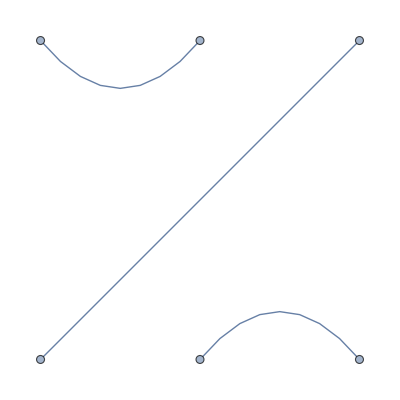
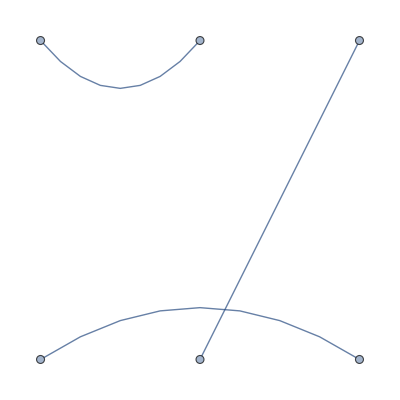
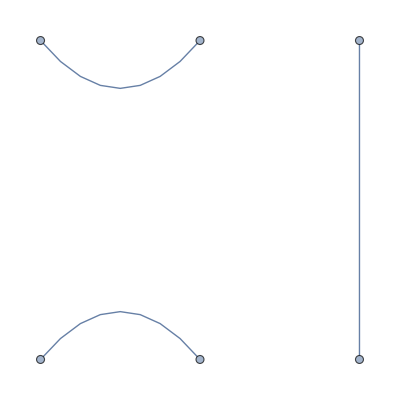
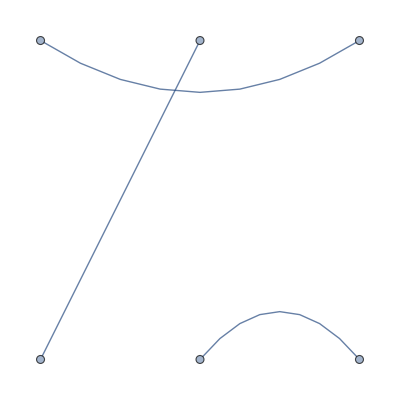
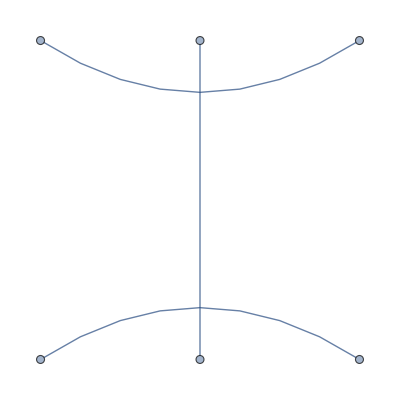
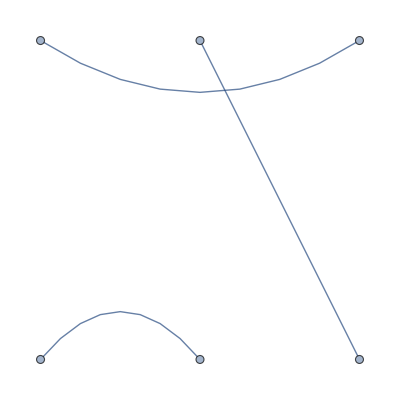
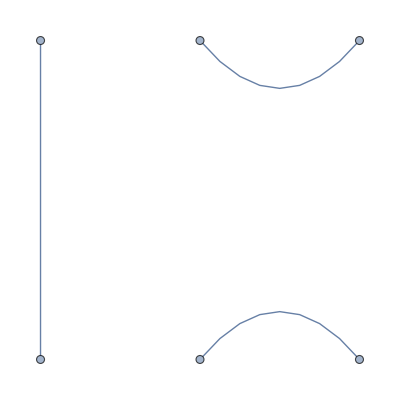
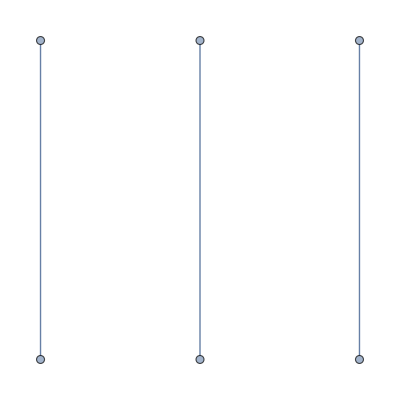
{-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g,-Graphics-_B_g}

{δ |   | i3
i4 |   g | i1 | i2
  |   g |   |  
i5 | i6,δ |   | i3
i5 |   g | i1 | i2
  |   g |   |  
i4 | i6,δ |   | i3
i6 |   g | i1 | i2
  |   g |   |  
i4 | i5,δ |   | i2
i4 |   g | i1 | i3
  |   g |   |  
i5 | i6,δ |   | i2
i5 |   g | i1 | i3
  |   g |   |  
i4 | i6,δ |   | i2
i6 |   g | i1 | i3
  |   g |   |  
i4 | i5,δ |   | i1
i4 |   g | i2 | i3
  |   g |   |  
i5 | i6,δ |   | i1
i4 |   δ |   | i2
i5 |   δ |   | i3
i6 |  ,δ |   | i1
i4 |   δ |   | i3
i5 |   δ |   | i2
i6 |  ,δ |   | i1
i5 |   g | i2 | i3
  |   g |   |  
i4 | i6,δ |   | i2
i4 |   δ |   | i1
i5 |   δ |   | i3
i6 |  ,δ |   | i3
i4 |   δ |   | i1
i5 |   δ |   | i2
i6 |  ,δ |   | i1
i6 |   g | i2 | i3
  |   g |   |  
i4 | i5,δ |   | i2
i4 |   δ |   | i3
i5 |   δ |   | i1
i6 |  ,δ |   | i3
i4 |   δ |   | i2
i5 |   δ |   | i1
i6 |  }

```mathematica
BrauerElements[3]
BrauerDiagram/@%
BrauerToTensor/@%
```

```mathematica
BrauerElements[4];
BrauerDiagram[#,ImageSize->30]&/@%
BrauerToTensor/@%
```

{(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g,(-Graphics-)_B_g}

{g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
i5 | i6 g |   |  
i7 | i8,g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
i5 | i7 g |   |  
i6 | i8,g | i1 | i2
  |   g | i3 | i4
  |   g |   |  
i5 | i8 g |   |  
i6 | i7,δ |   | i3
i5 |   δ |   | i4
i6 |   g | i1 | i2
  |   g |   |  
i7 | i8,δ |   | i3
i5 |   δ |   | i4
i7 |   g | i1 | i2
  |   g |   |  
i6 | i8,δ |   | i3
i5 |   δ |   | i4
i8 |   g | i1 | i2
  |   g |   |  
i6 | i7,δ |   | i4
i5 |   δ |   | i3
i6 |   g | i1 | i2
  |   g |   |  
i7 | i8,δ |   | i3
i6 |   δ |   | i4
i7 |   g | i1 | i2
  |   g |   |  
i5 | i8,δ |   | i3
i6 |   δ |   | i4
i8 |   g | i1 | i2
  |   g |   |  
i5 | i7,δ |   | i4
i5 |   δ |   | i3
i7 |   g | i1 | i2
  |   g |   |  
i6 | i8,δ |   | i4
i6 |   δ |   | i3
i7 |   g | i1 | i2
  |   g |   |  
i5 | i8,δ |   | i3
i7 |   δ |   | i4
i8 |   g | i1 | i2
  |   g |   |  
i5 | i6,δ |   | i4
i5 |   δ |   | i3
i8 |   g | i1 | i2
  |   g |   |  
i6 | i7,δ |   | i4
i6 |   δ |   | i3
i8 |   g | i1 | i2
  |   g |   |  
i5 | i7,δ |   | i4
i7 |   δ |   | i3
i8 |   g | i1 | i2
  |   g |   |  
i5 | i6,g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
i5 | i6 g |   |  
i7 | i8,g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
i5 | i7 g |   |  
i6 | i8,g | i1 | i3
  |   g | i2 | i4
  |   g |   |  
i5 | i8 g |   |  
i6 | i7,δ |   | i2
i5 |   δ |   | i4
i6 |   g | i1 | i3
  |   g |   |  
i7 | i8,δ |   | i2
i5 |   δ |   | i4
i7 |   g | i1 | i3
  |   g |   |  
i6 | i8,δ |   | i2
i5 |   δ |   | i4
i8 |   g | i1 | i3
  |   g |   |  
i6 | i7,δ |   | i4
i5 |   δ |   | i2
i6 |   g | i1 | i3
  |   g |   |  
i7 | i8,δ |   | i2
i6 |   δ |   | i4
i7 |   g | i1 | i3
  |   g |   |  
i5 | i8,δ |   | i2
i6 |   δ |   | i4
i8 |   g | i1 | i3
  |   g |   |  
i5 | i7,δ |   | i4
i5 |   δ |   | i2
i7 |   g | i1 | i3
  |   g |   |  
i6 | i8,δ |   | i4
i6 |   δ |   | i2
i7 |   g | i1 | i3
  |   g |   |  
i5 | i8,δ |   | i2
i7 |   δ |   | i4
i8 |   g | i1 | i3
  |   g |   |  
i5 | i6,δ |   | i4
i5 |   δ |   | i2
i8 |   g | i1 | i3
  |   g |   |  
i6 | i7,δ |   | i4
i6 |   δ |   | i2
i8 |   g | i1 | i3
  |   g |   |  
i5 | i7,δ |   | i4
i7 |   δ |   | i2
i8 |   g | i1 | i3
  |   g |   |  
i5 | i6,g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
i5 | i6 g |   |  
i7 | i8,g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
i5 | i7 g |   |  
i6 | i8,g | i1 | i4
  |   g | i2 | i3
  |   g |   |  
i5 | i8 g |   |  
i6 | i7,δ |   | i2
i5 |   δ |   | i3
i6 |   g | i1 | i4
  |   g |   |  
i7 | i8,δ |   | i2
i5 |   δ |   | i3
i7 |   g | i1 | i4
  |   g |   |  
i6 | i8,δ |   | i2
i5 |   δ |   | i3
i8 |   g | i1 | i4
  |   g |   |  
i6 | i7,δ |   | i3
i5 |   δ |   | i2
i6 |   g | i1 | i4
  |   g |   |  
i7 | i8,δ |   | i2
i6 |   δ |   | i3
i7 |   g | i1 | i4
  |   g |   |  
i5 | i8,δ |   | i2
i6 |   δ |   | i3
i8 |   g | i1 | i4
  |   g |   |  
i5 | i7,δ |   | i3
i5 |   δ |   | i2
i7 |   g | i1 | i4
  |   g |   |  
i6 | i8,δ |   | i3
i6 |   δ |   | i2
i7 |   g | i1 | i4
  |   g |   |  
i5 | i8,δ |   | i2
i7 |   δ |   | i3
i8 |   g | i1 | i4
  |   g |   |  
i5 | i6,δ |   | i3
i5 |   δ |   | i2
i8 |   g | i1 | i4
  |   g |   |  
i6 | i7,δ |   | i3
i6 |   δ |   | i2
i8 |   g | i1 | i4
  |   g |   |  
i5 | i7,δ |   | i3
i7 |   δ |   | i2
i8 |   g | i1 | i4
  |   g |   |  
i5 | i6,δ |   | i1
i5 |   δ |   | i4
i6 |   g | i2 | i3
  |   g |   |  
i7 | i8,δ |   | i1
i5 |   δ |   | i4
i7 |   g | i2 | i3
  |   g |   |  
i6 | i8,δ |   | i1
i5 |   δ |   | i4
i8 |   g | i2 | i3
  |   g |   |  
i6 | i7,δ |   | i1
i5 |   δ |   | i3
i6 |   g | i2 | i4
  |   g |   |  
i7 | i8,δ |   | i1
i5 |   δ |   | i3
i7 |   g | i2 | i4
  |   g |   |  
i6 | i8,δ |   | i1
i5 |   δ |   | i3
i8 |   g | i2 | i4
  |   g |   |  
i6 | i7,δ |   | i1
i5 |   δ |   | i2
i6 |   g | i3 | i4
  |   g |   |  
i7 | i8,δ |   | i1
i5 |   δ |   | i2
i6 |   δ |   | i3
i7 |   δ |   | i4
i8 |  ,δ |   | i1
i5 |   δ |   | i2
i6 |   δ |   | i4
i7 |   δ |   | i3
i8 |  ,δ |   | i1
i5 |   δ |   | i2
i7 |   g | i3 | i4
  |   g |   |  
i6 | i8,δ |   | i1
i5 |   δ |   | i3
i6 |   δ |   | i2
i7 |   δ |   | i4
i8 |  ,δ |   | i1
i5 |   δ |   | i4
i6 |   δ |   | i2
i7 |   δ |   | i3
i8 |  ,δ |   | i1
i5 |   δ |   | i2
i8 |   g | i3 | i4
  |   g |   |  
i6 | i7,δ |   | i1
i5 |   δ |   | i3
i6 |   δ |   | i4
i7 |   δ |   | i2
i8 |  ,δ |   | i1
i5 |   δ |   | i4
i6 |   δ |   | i3
i7 |   δ |   | i2
i8 |  ,δ |   | i4
i5 |   δ |   | i1
i6 |   g | i2 | i3
  |   g |   |  
i7 | i8,δ |   | i1
i6 |   δ |   | i4
i7 |   g | i2 | i3
  |   g |   |  
i5 | i8,δ |   | i1
i6 |   δ |   | i4
i8 |   g | i2 | i3
  |   g |   |  
i5 | i7,δ |   | i3
i5 |   δ |   | i1
i6 |   g | i2 | i4
  |   g |   |  
i7 | i8,δ |   | i1
i6 |   δ |   | i3
i7 |   g | i2 | i4
  |   g |   |  
i5 | i8,δ |   | i1
i6 |   δ |   | i3
i8 |   g | i2 | i4
  |   g |   |  
i5 | i7,δ |   | i2
i5 |   δ |   | i1
i6 |   g | i3 | i4
  |   g |   |  
i7 | i8,δ |   | i2
i5 |   δ |   | i1
i6 |   δ |   | i3
i7 |   δ |   | i4
i8 |  ,δ |   | i2
i5 |   δ |   | i1
i6 |   δ |   | i4
i7 |   δ |   | i3
i8 |  ,δ |   | i1
i6 |   δ |   | i2
i7 |   g | i3 | i4
  |   g |   |  
i5 | i8,δ |   | i3
i5 |   δ |   | i1
i6 |   δ |   | i2
i7 |   δ |   | i4
i8 |  ,δ |   | i4
i5 |   δ |   | i1
i6 |   δ |   | i2
i7 |   δ |   | i3
i8 |  ,δ |   | i1
i6 |   δ |   | i2
i8 |   g | i3 | i4
  |   g |   |  
i5 | i7,δ |   | i3
i5 |   δ |   | i1
i6 |   δ |   | i4
i7 |   δ |   | i2
i8 |  ,δ |   | i4
i5 |   δ |   | i1
i6 |   δ |   | i3
i7 |   δ |   | i2
i8 |  ,δ |   | i4
i5 |   δ |   | i1
i7 |   g | i2 | i3
  |   g |   |  
i6 | i8,δ |   | i4
i6 |   δ |   | i1
i7 |   g | i2 | i3
  |   g |   |  
i5 | i8,δ |   | i1
i7 |   δ |   | i4
i8 |   g | i2 | i3
  |   g |   |  
i5 | i6,δ |   | i3
i5 |   δ |   | i1
i7 |   g | i2 | i4
  |   g |   |  
i6 | i8,δ |   | i3
i6 |   δ |   | i1
i7 |   g | i2 | i4
  |   g |   |  
i5 | i8,δ |   | i1
i7 |   δ |   | i3
i8 |   g | i2 | i4
  |   g |   |  
i5 | i6,δ |   | i2
i5 |   δ |   | i1
i7 |   g | i3 | i4
  |   g |   |  
i6 | i8,δ |   | i2
i5 |   δ |   | i3
i6 |   δ |   | i1
i7 |   δ |   | i4
i8 |  ,δ |   | i2
i5 |   δ |   | i4
i6 |   δ |   | i1
i7 |   δ |   | i3
i8 |  ,δ |   | i2
i6 |   δ |   | i1
i7 |   g | i3 | i4
  |   g |   |  
i5 | i8,δ |   | i3
i5 |   δ |   | i2
i6 |   δ |   | i1
i7 |   δ |   | i4
i8 |  ,δ |   | i4
i5 |   δ |   | i2
i6 |   δ |   | i1
i7 |   δ |   | i3
i8 |  ,δ |   | i1
i7 |   δ |   | i2
i8 |   g | i3 | i4
  |   g |   |  
i5 | i6,δ |   | i3
i5 |   δ |   | i4
i6 |   δ |   | i1
i7 |   δ |   | i2
i8 |  ,δ |   | i4
i5 |   δ |   | i3
i6 |   δ |   | i1
i7 |   δ |   | i2
i8 |  ,δ |   | i4
i5 |   δ |   | i1
i8 |   g | i2 | i3
  |   g |   |  
i6 | i7,δ |   | i4
i6 |   δ |   | i1
i8 |   g | i2 | i3
  |   g |   |  
i5 | i7,δ |   | i4
i7 |   δ |   | i1
i8 |   g | i2 | i3
  |   g |   |  
i5 | i6,δ |   | i3
i5 |   δ |   | i1
i8 |   g | i2 | i4
  |   g |   |  
i6 | i7,δ |   | i3
i6 |   δ |   | i1
i8 |   g | i2 | i4
  |   g |   |  
i5 | i7,δ |   | i3
i7 |   δ |   | i1
i8 |   g | i2 | i4
  |   g |   |  
i5 | i6,δ |   | i2
i5 |   δ |   | i1
i8 |   g | i3 | i4
  |   g |   |  
i6 | i7,δ |   | i2
i5 |   δ |   | i3
i6 |   δ |   | i4
i7 |   δ |   | i1
i8 |  ,δ |   | i2
i5 |   δ |   | i4
i6 |   δ |   | i3
i7 |   δ |   | i1
i8 |  ,δ |   | i2
i6 |   δ |   | i1
i8 |   g | i3 | i4
  |   g |   |  
i5 | i7,δ |   | i3
i5 |   δ |   | i2
i6 |   δ |   | i4
i7 |   δ |   | i1
i8 |  ,δ |   | i4
i5 |   δ |   | i2
i6 |   δ |   | i3
i7 |   δ |   | i1
i8 |  ,δ |   | i2
i7 |   δ |   | i1
i8 |   g | i3 | i4
  |   g |   |  
i5 | i6,δ |   | i3
i5 |   δ |   | i4
i6 |   δ |   | i2
i7 |   δ |   | i1
i8 |  ,δ |   | i4
i5 |   δ |   | i3
i6 |   δ |   | i2
i7 |   δ |   | i1
i8 |  }

```mathematica
(** Parametrization of the symmetric group conjugacy class in Brauer ***)
```

```mathematica
BrauerTableaux[4]
TableauForm/@(Flatten@%)
```

{{{{1,2,3,3}}_Tab,{{1,3,2,3}}_Tab,{{1,2,3},{3}}_Tab,{{1,2},{3,3}}_Tab,{{1,2},{3},{3}}_Tab},{{{1,2,1,2}}_Tab,{{1,2},{1,2}}_Tab}}

{1 | 2 | 3 | 3,1 | 3 | 2 | 3,1 | 2 | 3
3 |  | ,1 | 2
3 | 3,1 | 2
3 | 
3 | ,1 | 2 | 1 | 2,1 | 2
1 | 2}

```mathematica
BrauerTableaux[4,SymmetricGroup->True]
TableauForm/@(Flatten@%)
```

{{{{3,3,3,3}}_Tab,{{3,3,3},{3}}_Tab,{{3,3},{3,3}}_Tab,{{3,3},{3},{3}}_Tab,{{3},{3},{3},{3}}_Tab},{{{{1,2,3,3}}_Tab,{{1,3,2,3}}_Tab,{{1,2,3},{3}}_Tab,{{1,2},{3,3}}_Tab,{{1,2},{3},{3}}_Tab},{{{1,2,1,2}}_Tab,{{1,2},{1,2}}_Tab}}}

{3 | 3 | 3 | 3,3 | 3 | 3
3 |  | ,3 | 3
3 | 3,3 | 3
3 | 
3 | ,3
3
3
3,1 | 2 | 3 | 3,1 | 3 | 2 | 3,1 | 2 | 3
3 |  | ,1 | 2
3 | 3,1 | 2
3 | 
3 | ,1 | 2 | 1 | 2,1 | 2
1 | 2}

The f-traceless projector can be expended in terms of the BrauerTableaux : 1-traceless projector projects arbitrary tensors on the space of traceless tensors aka harmonic tensors.

```mathematica
(** Trace and Traceless projectors ***)
```

```mathematica
?TraceLessProjector
```

```mathematica
TraceLessProjector[3,1];
TableauForm/@%
```

(1 | 2 | 3)/((-1+d) (2+d))-((1+d) 1 | 2
3 |)/((-1+d) (2+d))+3
3
3

```mathematica
TraceLessProjector[3,1];
BrauerToTensor@%
```

δ |   | i1
i4 |   δ |   | i2
i5 |   δ |   | i3
i6 |  +(δ |   | i2
i6 |   g | i1 | i3
  |   g |   |  
i4 | i5+δ |   | i1
i6 |   g | i2 | i3
  |   g |   |  
i4 | i5+δ |   | i3
i5 |   g | i1 | i2
  |   g |   |  
i4 | i6+δ |   | i1
i5 |   g | i2 | i3
  |   g |   |  
i4 | i6+δ |   | i3
i4 |   g | i1 | i2
  |   g |   |  
i5 | i6+δ |   | i2
i4 |   g | i1 | i3
  |   g |   |  
i5 | i6)/((-1+d) (2+d))-((1+d) (δ |   | i3
i6 |   g | i1 | i2
  |   g |   |  
i4 | i5+δ |   | i2
i5 |   g | i1 | i3
  |   g |   |  
i4 | i6+δ |   | i1
i4 |   g | i2 | i3
  |   g |   |  
i5 | i6))/((-1+d) (2+d))

```mathematica
TraceLessProjector[4,1];
TableauForm/@%
```

-((2+3 d) 1 | 2 | 1 | 2)/((-2+d) (-1+d) (2+d) (4+d))-(1 | 2 | 3 | 3)/((-2+d) (2+d) (4+d))-(2 1 | 3 | 2 | 3)/((-2+d) d (4+d))+((6+3 d+d^2) 1 | 2
1 | 2)/((-2+d) (-1+d) (2+d) (4+d))+(4 1 | 2
3 | 3)/((-2+d) d (2+d) (4+d))+((3+d) 1 | 2 | 3
3 |  |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) 1 | 2
3 | 
3 |)/((-2+d) d (2+d) (4+d))+3
3
3
3

```mathematica
TraceLessProjector[4,1];
TableauForm/@%
```

-((2+3 d) 1 | 2 | 1 | 2)/((-2+d) (-1+d) (2+d) (4+d))-(1 | 2 | 3 | 3)/((-2+d) (2+d) (4+d))-(2 1 | 3 | 2 | 3)/((-2+d) d (4+d))+((6+3 d+d^2) 1 | 2
1 | 2)/((-2+d) (-1+d) (2+d) (4+d))+(4 1 | 2
3 | 3)/((-2+d) d (2+d) (4+d))+((3+d) 1 | 2 | 3
3 |  |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) 1 | 2
3 | 
3 |)/((-2+d) d (2+d) (4+d))+3
3
3
3

```mathematica
TraceLessProjector[4,2];
TableauForm/@%
```

-(1 | 2 | 1 | 2)/((-1+d) d (2+d))-((2+3 d) 1 | 2 | 1 | 2)/((-2+d) (-1+d) (2+d) (4+d))-(1 | 2 | 3 | 3)/((-2+d) (2+d) (4+d))-(2 1 | 3 | 2 | 3)/((-2+d) d (4+d))+((1+d) 1 | 2
1 | 2)/((-1+d) d (2+d))+((6+3 d+d^2) 1 | 2
1 | 2)/((-2+d) (-1+d) (2+d) (4+d))+(4 1 | 2
3 | 3)/((-2+d) d (2+d) (4+d))+((3+d) 1 | 2 | 3
3 |  |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) 1 | 2
3 | 
3 |)/((-2+d) d (2+d) (4+d))

```mathematica
TraceLessProjector[5,1];
TableauForm/@%
```

((6+5 d) 1 | 2 | 1 | 2 | 3)/((-3+d) (-2+d) (1+d) (4+d) (6+d))+(d (-4-4 d+d^2) 1 | 2 | 3 | 3 | 3)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+((-12+2 d+3 d^2) 1 | 3 | 2 | 3 | 3)/((-3+d) (-2+d) (-1+d) (1+d) (4+d) (6+d))-((18+5 d+d^2) 1 | 2 | 3
1 | 2 |)/((-3+d) (-2+d) (1+d) (4+d) (6+d))-(4 (-12+2 d+3 d^2) 1 | 2 | 3
3 | 3 |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-(6 (-4-4 d+d^2) 3 | 3 | 3
1 | 2 |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-((-18+11 d+3 d^2) 1 | 2 | 1 | 2
3 |  |  |)/((-3+d) (-2+d) (1+d) (4+d) (6+d))-((24-4 d-10 d^2+3 d^3+d^4) 1 | 2 | 3 | 3
3 |  |  |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-(2 d (-11+3 d+d^2) 1 | 3 | 2 | 3
3 |  |  |)/((-3+d) (-2+d) (-1+d) (1+d) (4+d) (6+d))+((-6+3 d+6 d^2+d^3) 1 | 2
1 | 2
3 |)/((-3+d) (-2+d) (1+d) (4+d) (6+d))+(4 d 1 | 2
3 | 3
3 |)/((-3+d) (-2+d) (1+d) (2+d) (6+d))+((48+4 d-40 d^2-5 d^3+6 d^4+d^5) 1 | 2 | 3
3 |  | 
3 |  |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-(d (148+4 d-71 d^2-5 d^3+7 d^4+d^5) 1 | 2
3 | 
3 | 
3 |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+3
3
3
3
3

```mathematica
?TraceProjector
```

fmax traceprojector is much faster then any other projectors because it uses Weingarten calculus ..

```mathematica
TraceProjector[4,2];
TableauForm/@%
```

-(1 | 2 | 1 | 2)/((-1+d) d (2+d))+((1+d) 1 | 2
1 | 2)/((-1+d) d (2+d))

```mathematica
TraceProjector[5,2];
TableauForm/@%
```

(2 1 | 2 | 1 | 2 | 3)/((-2+d) (-1+d) (2+d) (4+d))-(1 | 2 | 3
1 | 2 |)/((-2+d) (-1+d) (4+d))-(1 | 2 | 1 | 2
3 |  |  |)/((-2+d) (-1+d) (4+d))+((-2+3 d+d^2) 1 | 2
1 | 2
3 |)/((-2+d) (-1+d) (2+d) (4+d))

```mathematica
TraceProjector[6,3];
TableauForm/@%
```

(2 1 | 2 | 1 | 2 | 1 | 2)/((-2+d) (-1+d) d (2+d) (4+d))-(1 | 2 | 1 | 2
1 | 2 |  |)/((-2+d) (-1+d) d (4+d))+((-2+3 d+d^2) 1 | 2
1 | 2
1 | 2)/((-2+d) (-1+d) d (2+d) (4+d))

```mathematica
TraceProjector[7,3];
TableauForm/@%
```

-((6+5 d) 1 | 2 | 1 | 2 | 1 | 2 | 3)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+((18+5 d+d^2) 1 | 2 | 1 | 2
1 | 2 | 3 |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+(2 d 1 | 2 | 1 | 2 | 3
1 | 2 |  |  |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (6+d))+(2 d 1 | 2 | 1 | 2 | 1 | 2
3 |  |  |  |  |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (6+d))-((-6+3 d+6 d^2+d^3) 1 | 2 | 3
1 | 2 | 
1 | 2 |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))-((-6+3 d+6 d^2+d^3) 1 | 2 | 1 | 2
1 | 2 |  | 
3 |  |  |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (4+d) (6+d))+((3+d) (1+6 d+d^2) 1 | 2
1 | 2
1 | 2
3 |)/((-3+d) (-1+d) (1+d) (2+d) (4+d) (6+d))

```mathematica
TraceProjector[8,4];
TableauForm/@%
```

-((6+5 d) 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2)/((-3+d) (-2+d) (-1+d) d (1+d) (2+d) (4+d) (6+d))+((18+5 d+d^2) 1 | 2 | 1 | 2
1 | 2 | 1 | 2)/((-3+d) (-2+d) (-1+d) d (1+d) (2+d) (4+d) (6+d))+(2 1 | 2 | 1 | 2 | 1 | 2
1 | 2 |  |  |  |)/((-3+d) (-2+d) (-1+d) (1+d) (2+d) (6+d))-((-6+3 d+6 d^2+d^3) 1 | 2 | 1 | 2
1 | 2 |  | 
1 | 2 |  |)/((-3+d) (-2+d) (-1+d) d (1+d) (2+d) (4+d) (6+d))+((3+d) (1+6 d+d^2) 1 | 2
1 | 2
1 | 2
1 | 2)/((-3+d) (-1+d) d (1+d) (2+d) (4+d) (6+d))

```mathematica
(******** Action of the Traceless projector on tensors *********)
```

```mathematica
?ToTracelessTensor
```

```mathematica
DefTensor[X3[-i1,-i2 ,-i3],M,PrintAs->"X^(3)"]
DefTensor[X4[-i1,-i2 ,-i3,-i4],M,PrintAs->"X^(4)"]
DefTensor[X5[-i1,-i2 ,-i3,-i4,-i5],M,PrintAs->"X^(5)"]
```

** DefTensor: Defining tensor X3[-i1,-i2,-i3].

** DefTensor: Defining tensor X4[-i1,-i2,-i3,-i4].

** DefTensor: Defining tensor X5[-i1,-i2,-i3,-i4,-i5].

```mathematica
ToTracelessTensor[X3[-i1,-i2 ,-i3],1]
g[i1,i2]*%//ToCanonical//ContractMetric//Simplify
g[i1,i3]*%//ToCanonical//ContractMetric//Simplify
g[i2,i3]*%//ToCanonical//ContractMetric//Simplify
```

X^(3) |   |   |  
i1 | i2 | i3+g |   |  
i2 | i3 (-((1+d) X^(3) |   |   | i4
i1 | i4 |)/((-1+d) (2+d))+(X^(3) |   |   | i4
i4 | i1 |)/((-1+d) (2+d))+(X^(3) |   | i4 |  
i4 |   | i1)/((-1+d) (2+d)))+g |   |  
i1 | i3 ((X^(3) |   |   | i4
i2 | i4 |)/((-1+d) (2+d))-((1+d) X^(3) |   |   | i4
i4 | i2 |)/((-1+d) (2+d))+(X^(3) |   | i4 |  
i4 |   | i2)/((-1+d) (2+d)))+g |   |  
i1 | i2 ((X^(3) |   |   | i4
i3 | i4 |)/((-1+d) (2+d))+(X^(3) |   |   | i4
i4 | i3 |)/((-1+d) (2+d))-((1+d) X^(3) |   | i4 |  
i4 |   | i3)/((-1+d) (2+d)))

0

0

0

```mathematica
ToTracelessTensor[X4[-i1,-i2 ,-i3,-i4],1]
g[i1,i2]*%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i1,i3]*%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i1,i4]*%%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i2,i3]*%%%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i2,i4]*%%%%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i3,i4]*%%%%%//ToCanonical//ContractMetric//SameDummies//Simplify
```

X^(4) |   |   |   |  
i1 | i2 | i3 | i4+g |   |  
i3 | i4 (-((-4+4 d^2+d^3) X^(4) |   |   |   | i5
i1 | i2 | i5 |)/((-2+d) d (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i1 | i5 | i2 |)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   | i5 |  
i1 | i5 |   | i2)/((-2+d) (2+d) (4+d))+(4 X^(4) |   |   |   | i5
i2 | i1 | i5 |)/((-2+d) d (2+d) (4+d))-(X^(4) |   |   |   | i5
i2 | i5 | i1 |)/((-2+d) (2+d) (4+d))-(X^(4) |   |   | i5 |  
i2 | i5 |   | i1)/((-2+d) (2+d) (4+d))-(X^(4) |   |   |   | i5
i5 | i1 | i2 |)/((-2+d) (2+d) (4+d))-(X^(4) |   |   | i5 |  
i5 | i1 |   | i2)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i5 | i2 | i1 |)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   | i5 |  
i5 | i2 |   | i1)/((-2+d) (2+d) (4+d))-(2 X^(4) |   | i5 |   |  
i5 |   | i1 | i2)/((-2+d) d (4+d))-(2 X^(4) |   | i5 |   |  
i5 |   | i2 | i1)/((-2+d) d (4+d)))+g |   |  
i2 | i4 (((3+d) X^(4) |   |   |   | i5
i1 | i3 | i5 |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) X^(4) |   |   |   | i5
i1 | i5 | i3 |)/((-2+d) d (2+d) (4+d))+((3+d) X^(4) |   |   | i5 |  
i1 | i5 |   | i3)/((-2+d) (2+d) (4+d))-(X^(4) |   |   |   | i5
i3 | i1 | i5 |)/((-2+d) (2+d) (4+d))+(4 X^(4) |   |   |   | i5
i3 | i5 | i1 |)/((-2+d) d (2+d) (4+d))-(X^(4) |   |   | i5 |  
i3 | i5 |   | i1)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i5 | i1 | i3 |)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   | i5 |  
i5 | i1 |   | i3)/((-2+d) d (4+d))-(X^(4) |   |   |   | i5
i5 | i3 | i1 |)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   | i5 |  
i5 | i3 |   | i1)/((-2+d) d (4+d))-(X^(4) |   | i5 |   |  
i5 |   | i1 | i3)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   | i5 |   |  
i5 |   | i3 | i1)/((-2+d) (2+d) (4+d)))+g |   |  
i2 | i3 (((3+d) X^(4) |   |   |   | i5
i1 | i4 | i5 |)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i1 | i5 | i4 |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) X^(4) |   |   | i5 |  
i1 | i5 |   | i4)/((-2+d) d (2+d) (4+d))-(X^(4) |   |   |   | i5
i4 | i1 | i5 |)/((-2+d) (2+d) (4+d))-(X^(4) |   |   |   | i5
i4 | i5 | i1 |)/((-2+d) (2+d) (4+d))+(4 X^(4) |   |   | i5 |  
i4 | i5 |   | i1)/((-2+d) d (2+d) (4+d))-(2 X^(4) |   |   |   | i5
i5 | i1 | i4 |)/((-2+d) d (4+d))+((3+d) X^(4) |   |   | i5 |  
i5 | i1 |   | i4)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   |   | i5
i5 | i4 | i1 |)/((-2+d) d (4+d))-(X^(4) |   |   | i5 |  
i5 | i4 |   | i1)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   | i5 |   |  
i5 |   | i1 | i4)/((-2+d) (2+d) (4+d))-(X^(4) |   | i5 |   |  
i5 |   | i4 | i1)/((-2+d) (2+d) (4+d)))+g |   |  
i1 | i2 (-(2 X^(4) |   |   |   | i5
i3 | i4 | i5 |)/((-2+d) d (4+d))-(X^(4) |   |   |   | i5
i3 | i5 | i4 |)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   | i5 |  
i3 | i5 |   | i4)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   |   | i5
i4 | i3 | i5 |)/((-2+d) d (4+d))+((3+d) X^(4) |   |   |   | i5
i4 | i5 | i3 |)/((-2+d) (2+d) (4+d))-(X^(4) |   |   | i5 |  
i4 | i5 |   | i3)/((-2+d) (2+d) (4+d))-(X^(4) |   |   |   | i5
i5 | i3 | i4 |)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   | i5 |  
i5 | i3 |   | i4)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i5 | i4 | i3 |)/((-2+d) (2+d) (4+d))-(X^(4) |   |   | i5 |  
i5 | i4 |   | i3)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) X^(4) |   | i5 |   |  
i5 |   | i3 | i4)/((-2+d) d (2+d) (4+d))+(4 X^(4) |   | i5 |   |  
i5 |   | i4 | i3)/((-2+d) d (2+d) (4+d))+g |   |  
i3 | i4 (((6+3 d+d^2) X^(4) |   | i5 |   | i6
i5 |   | i6 |)/((-2+d) (-1+d) (2+d) (4+d))-((2+3 d) X^(4) |   |   | i5 | i6
i5 | i6 |   |)/((-2+d) (-1+d) (2+d) (4+d))-((2+3 d) X^(4) |   |   | i6 | i5
i5 | i6 |   |)/((-2+d) (-1+d) (2+d) (4+d))))+g |   |  
i1 | i3 (-(X^(4) |   |   |   | i5
i2 | i4 | i5 |)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   |   | i5
i2 | i5 | i4 |)/((-2+d) d (4+d))+((3+d) X^(4) |   |   | i5 |  
i2 | i5 |   | i4)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i4 | i2 | i5 |)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   |   | i5
i4 | i5 | i2 |)/((-2+d) d (4+d))-(X^(4) |   |   | i5 |  
i4 | i5 |   | i2)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i5 | i2 | i4 |)/((-2+d) (2+d) (4+d))-((-4+4 d^2+d^3) X^(4) |   |   | i5 |  
i5 | i2 |   | i4)/((-2+d) d (2+d) (4+d))-(X^(4) |   |   |   | i5
i5 | i4 | i2 |)/((-2+d) (2+d) (4+d))+(4 X^(4) |   |   | i5 |  
i5 | i4 |   | i2)/((-2+d) d (2+d) (4+d))+((3+d) X^(4) |   | i5 |   |  
i5 |   | i2 | i4)/((-2+d) (2+d) (4+d))-(X^(4) |   | i5 |   |  
i5 |   | i4 | i2)/((-2+d) (2+d) (4+d))+g |   |  
i2 | i4 (-((2+3 d) X^(4) |   | i5 |   | i6
i5 |   | i6 |)/((-2+d) (-1+d) (2+d) (4+d))+((6+3 d+d^2) X^(4) |   |   | i5 | i6
i5 | i6 |   |)/((-2+d) (-1+d) (2+d) (4+d))-((2+3 d) X^(4) |   |   | i6 | i5
i5 | i6 |   |)/((-2+d) (-1+d) (2+d) (4+d))))+g |   |  
i1 | i4 (-(X^(4) |   |   |   | i5
i2 | i3 | i5 |)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   |   |   | i5
i2 | i5 | i3 |)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   | i5 |  
i2 | i5 |   | i3)/((-2+d) d (4+d))+((3+d) X^(4) |   |   |   | i5
i3 | i2 | i5 |)/((-2+d) (2+d) (4+d))-(X^(4) |   |   |   | i5
i3 | i5 | i2 |)/((-2+d) (2+d) (4+d))-(2 X^(4) |   |   | i5 |  
i3 | i5 |   | i2)/((-2+d) d (4+d))-((-4+4 d^2+d^3) X^(4) |   |   |   | i5
i5 | i2 | i3 |)/((-2+d) d (2+d) (4+d))+((3+d) X^(4) |   |   | i5 |  
i5 | i2 |   | i3)/((-2+d) (2+d) (4+d))+(4 X^(4) |   |   |   | i5
i5 | i3 | i2 |)/((-2+d) d (2+d) (4+d))-(X^(4) |   |   | i5 |  
i5 | i3 |   | i2)/((-2+d) (2+d) (4+d))-(X^(4) |   | i5 |   |  
i5 |   | i2 | i3)/((-2+d) (2+d) (4+d))+((3+d) X^(4) |   | i5 |   |  
i5 |   | i3 | i2)/((-2+d) (2+d) (4+d))+g |   |  
i2 | i3 (-((2+3 d) X^(4) |   | i5 |   | i6
i5 |   | i6 |)/((-2+d) (-1+d) (2+d) (4+d))-((2+3 d) X^(4) |   |   | i5 | i6
i5 | i6 |   |)/((-2+d) (-1+d) (2+d) (4+d))+((6+3 d+d^2) X^(4) |   |   | i6 | i5
i5 | i6 |   |)/((-2+d) (-1+d) (2+d) (4+d))))

0

0

0

«3 more identical outputs»

2-traceless projector projects arbitrary tensors on the space of double traceless tensors :

```mathematica
ToTracelessTensor[X4[-i1,-i2 ,-i3,-i4],2];
g[i1,i2]*%//ToCanonical//ContractMetric//SameDummies//Simplify
```

(g |   |  
i3 | i4 X^(4) |   | i1 |   | i2
i1 |   | i2 |)/d-X^(4) |   | i1 |   |  
i1 |   | i3 | i4

```mathematica
ToTracelessTensor[X4[-i1,-i2 ,-i3,-i4],2];
g[i1,i2]*g[i2,i3]*%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i1,i3]*g[i2,i4]*%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i1,i4]*g[i2,i3]*%%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i2,i3]*g[i1,i4]%%%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i2,i4]*g[i1,i3]*%%%%%//ToCanonical//ContractMetric//SameDummies//Simplify
g[i3,i4]*g[i1,i2]*%%%%%%//ToCanonical//ContractMetric//SameDummies//Simplify
```

1/((-2+d) d (2+d) (4+d))(-(4-14 d-4 d^2+4 d^3+d^4) X^(4) |   | i1 | i2 |  
i1 |   |   | i4-4 X^(4) |   | i1 |   | i2
i1 |   | i4 |  -2 d X^(4) |   | i1 |   | i2
i1 |   | i4 |  -d X^(4) |   | i2 | i1 |  
i1 |   |   | i4-d X^(4) |   | i2 |   | i1
i1 |   | i4 |  +2 (-4+d^2) δ | i2 |  
  | i4 (X^(4) |   | i1 |   | i3
i1 |   | i3 |  +X^(4) |   |   | i1 | i3
i1 | i3 |   |  +X^(4) |   |   | i3 | i1
i1 | i3 |   |  )+3 d X^(4) |   |   | i1 | i2
i1 | i4 |   |  +d^2 X^(4) |   |   | i1 | i2
i1 | i4 |   |  +3 d X^(4) |   |   | i2 | i1
i1 | i4 |   |  +d^2 X^(4) |   |   | i2 | i1
i1 | i4 |   |  +3 d X^(4) | i2 |   | i1 |  
  | i1 |   | i4+d^2 X^(4) | i2 |   | i1 |  
  | i1 |   | i4+3 d X^(4) | i2 |   |   | i1
  | i1 | i4 |  +d^2 X^(4) | i2 |   |   | i1
  | i1 | i4 |  +4 X^(4) | i2 |   |   | i1
  | i4 | i1 |  -4 d^2 X^(4) | i2 |   |   | i1
  | i4 | i1 |  -d^3 X^(4) | i2 |   |   | i1
  | i4 | i1 |  -d X^(4) |   |   | i1 | i2
i4 | i1 |   |  -d X^(4) |   |   | i2 | i1
i4 | i1 |   |  +4 X^(4) |   | i2 |   | i1
i4 |   | i1 |  )

0

0

0

«2 more identical outputs»

The Weyl tensor for the Levi-Civita tensor

```mathematica
Riemanncd[-i1,-i2,-i3,i4]
Collect[ToTracelessTensor[%,1]//ToCanonical,{_RicciScalarcd,_delta,_g,_Riccicd},Factor]
```

R[∇^(g)] |   |   |   | i4
i1 | i2 | i3 |

-(δ |   | i4
i2 |   R[∇^(g)] |   |  
i1 | i3)/(-2+d)+(g |   |  
i2 | i3 R[∇^(g)] |   | i4
i1 |)/(-2+d)+(δ |   | i4
i1 |   R[∇^(g)] |   |  
i2 | i3)/(-2+d)-(g |   |  
i1 | i3 R[∇^(g)] |   | i4
i2 |)/(-2+d)+((δ |   | i4
i2 |   g |   |  
i1 | i3)/((-2+d) (-1+d))-(δ |   | i4
i1 |   g |   |  
i2 | i3)/((-2+d) (-1+d))) R[∇^(g)]+R[∇^(g)] |   |   |   | i4
i1 | i2 | i3 |

```mathematica
Weylcd[-i1,-i2,-i3,i4]
Collect[WeylToRiemann@%,{_RicciScalarcd,_delta,_g,_Riccicd},Factor]
```

W[∇^(g)] |   |   |   | i4
i1 | i2 | i3 |

-(δ |   | i4
i2 |   R[∇^(g)] |   |  
i1 | i3)/(-2+d)+(g |   |  
i3 | i2 R[∇^(g)] |   | i4
i1 |)/(-2+d)+(δ |   | i4
i1 |   R[∇^(g)] |   |  
i2 | i3)/(-2+d)-(g |   |  
i3 | i1 R[∇^(g)] |   | i4
i2 |)/(-2+d)+((δ |   | i4
i2 |   g |   |  
i3 | i1)/((-2+d) (-1+d))-(δ |   | i4
i1 |   g |   |  
i3 | i2)/((-2+d) (-1+d))) R[∇^(g)]+R[∇^(g)] |   |   |   | i4
i1 | i2 | i3 |

The conformal Weyl tensor (totally traceless part of Riemann) for an arbitrary connection) : See xMAG for a more detailed treatment

```mathematica
DefCovD[CD[-i1],SymbolOfCovD->{"|","∇^(Γ) "},Torsion->True]
```

** DefCovD: Defining covariant derivative CD[-i1].

** DefTensor: Defining torsion tensor TorsionCD[i1,-i2,-i3].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCD[i1,-i2,-i3].

** DefTensor: Defining Riemann tensor RiemannCD[-i1,-i2,-i3,i4]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-i1,-i2].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

```mathematica
RiemannCD[-i1,-i2,-i3,i4]
Collect[ToTracelessTensor[%,1]//ToCanonical,{_RicciScalarcd,_delta,_g,_Riccicd},Factor]
```

R[∇^(Γ)] |   |   |   | i4
i1 | i2 | i3 |

R[∇^(Γ)] |   |   |   | i4
i1 | i2 | i3 |  -(δ |   | i4
i3 |   (-R[∇^(Γ)] |   |  
i1 | i2+R[∇^(Γ)] |   |  
i2 | i1+d R[∇^(Γ)] |   |   |   | i5
i1 | i2 | i5 |  -R[∇^(Γ)] |   |   | i5 |  
i1 | i5 |   | i2+R[∇^(Γ)] |   |   | i5 |  
i2 | i5 |   | i1))/((-2+d) (2+d))+δ |   | i4
i2 |   ((g |   |  
i1 | i3 R[∇^(Γ)] |   | i5
i5 |)/((-2+d) (-1+d))-(-R[∇^(Γ)] |   |  
i1 | i3+d R[∇^(Γ)] |   |  
i1 | i3+d^2 R[∇^(Γ)] |   |  
i1 | i3-R[∇^(Γ)] |   |  
i3 | i1-d R[∇^(Γ)] |   |   |   | i5
i1 | i3 | i5 |  -R[∇^(Γ)] |   |   | i5 |  
i1 | i5 |   | i3-d R[∇^(Γ)] |   |   | i5 |  
i1 | i5 |   | i3-R[∇^(Γ)] |   |   | i5 |  
i3 | i5 |   | i1)/((-2+d) d (2+d)))+δ |   | i4
i1 |   (-(g |   |  
i2 | i3 R[∇^(Γ)] |   | i5
i5 |)/((-2+d) (-1+d))+(-R[∇^(Γ)] |   |  
i2 | i3+d R[∇^(Γ)] |   |  
i2 | i3+d^2 R[∇^(Γ)] |   |  
i2 | i3-R[∇^(Γ)] |   |  
i3 | i2-d R[∇^(Γ)] |   |   |   | i5
i2 | i3 | i5 |  -R[∇^(Γ)] |   |   | i5 |  
i2 | i5 |   | i3-d R[∇^(Γ)] |   |   | i5 |  
i2 | i5 |   | i3-R[∇^(Γ)] |   |   | i5 |  
i3 | i5 |   | i2)/((-2+d) d (2+d)))-(g |   |  
i2 | i3 (-R[∇^(Γ)] |   | i4
i1 |  -d R[∇^(Γ)] |   | i4
i1 |  -R[∇^(Γ)] | i4 |  
  | i1-d R[∇^(Γ)] |   | i4 |   | i5
i1 |   | i5 |  -R[∇^(Γ)] |   |   | i5 | i4
i1 | i5 |   |  +d R[∇^(Γ)] |   |   | i5 | i4
i1 | i5 |   |  +d^2 R[∇^(Γ)] |   |   | i5 | i4
i1 | i5 |   |  -R[∇^(Γ)] | i4 |   | i5 |  
  | i5 |   | i1))/((-2+d) d (2+d))+(g |   |  
i1 | i3 (-R[∇^(Γ)] |   | i4
i2 |  -d R[∇^(Γ)] |   | i4
i2 |  -R[∇^(Γ)] | i4 |  
  | i2-d R[∇^(Γ)] |   | i4 |   | i5
i2 |   | i5 |  -R[∇^(Γ)] |   |   | i5 | i4
i2 | i5 |   |  +d R[∇^(Γ)] |   |   | i5 | i4
i2 | i5 |   |  +d^2 R[∇^(Γ)] |   |   | i5 | i4
i2 | i5 |   |  -R[∇^(Γ)] | i4 |   | i5 |  
  | i5 |   | i2))/((-2+d) d (2+d))